```mathematica
Grid[{{-Graphics-,"Anno Accademico 2017/18"}},ItemStyle->{Automatic,{1->{FontFamily->"Roboto Condensed",FontSize->20}}},Frame-> True,FrameStyle->{RGBColor[0.94,0.94,0.94]},Alignment->{{Left,Right}},Spacings->10,ItemSize-> Fit]
```

-Graphics- | Anno Accademico 2017/18

```mathematica
Grid[{{"Sistemi Lineari e Metodo di Gauss"}},ItemSize->Fit,Frame->True, FrameStyle->{RGBColor[0.13,0.52,0.96]},Spacings->{5,7},Background->{RGBColor[0.84,0.93,0.98]},ItemStyle->{Automatic, {1-> {FontFamily-> "Roboto Condensed", FontSize->40, FontColor->RGBColor[0.13,0.52,0.96]}}}]
```

Sistemi Lineari e Metodo di Gauss

```mathematica
Grid[{{-Graphics-, Column[{Style["Progetto D'Esame:", Red],"Matematica Computazionale (LM Informatica)\nCalcolo Numerico e Software Didattico (LM Matematica)","Sara Annese\nLaura Cappelli\nMatteo Del Vecchio\nMatteo Marchesini\nDaniele Rossi\nSilvia Scibilia"},Frame->None,Spacings->1]}}, ItemSize->Fit, Frame->None, Alignment->{{Right, Left}},Spacings->3, ItemStyle->{Automatic, {1-> {FontFamily->"Roboto Condensed", FontSize-> 18}}}]
```

-Graphics- | Progetto D'Esame:
Matematica Computazionale (LM Informatica)
Calcolo Numerico e Software Didattico (LM Matematica)
Sara Annese
Laura Cappelli
Matteo Del Vecchio
Matteo Marchesini
Daniele Rossi
Silvia Scibilia

```mathematica
forwardTag = "ReadySetGoTitle";
forwardButton := Hyperlink[Button[-Graphics-, ImageSize->{50,50}, Appearance->{None}],{"Home.nb",forwardTag}];
forwardLink := Hyperlink["Avanti", {"Home.nb", forwardTag},BaseStyle->RGBColor[0.2,0.6,0.86]];
appendiceLink = Hyperlink["Appendice", {"Home.nb", "Appendice"}, BaseStyle->RGBColor[0.2,0.6,0.86]];
bibliografiaLink = Hyperlink["Bibliografia", {"Home.nb", "Bibliografia"}, BaseStyle->RGBColor[0.2,0.6,0.86]];
navHome := Grid[{{appendiceLink,bibliografiaLink,forwardLink,forwardButton}},Alignment->{{Center, Center, Right, Left}}, ItemSize->{{Scaled[0.2],Scaled[0.25],Scaled[0.5],Scaled[0.05]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navHome
Clear[forwardTag];
```

AppendiceHome.nbAppendiceHome.nbHyperlinkHyperlinkActive | BibliografiaHome.nbBibliografiaHome.nbHyperlinkHyperlinkActive | AvantiHome.nbReadySetGoTitleHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbReadySetGoTitleHome.nb

### Ready, Set, Go!

```mathematica
SetDirectory[NotebookDirectory[]]; Get["GaussLinearSystemsPackage.m"];
```

#### Valutazione del notebook

```mathematica
Grid[{{"Per poter utilizzare il notebook, esso deve essere valutato.\nClicca in alto su \"Evaluate\" e poi su \"Evaluate Notebook\", come mostrato nell'immagine."},{Import["images/evaluation.gif", "Animation"]}},ItemSize->Fit, ItemStyle->Directive[FontFamily->"Roboto Condensed",FontSize->24,TextAlignment->Center],Spacings->{2,2}]
```

Per poter utilizzare il notebook, esso deve essere valutato.
Clicca in alto su "Evaluate" e poi su "Evaluate Notebook", come mostrato nell'immagine.

```mathematica
backTag = "Homepage";
forwardTag = "BlackboardHeader";
backButton := Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{50,50}],{"Home.nb",backTag}];
backLink := Hyperlink["Indietro", {"Home.nb", backTag},BaseStyle->RGBColor[0.2,0.6,0.86]];

navAvantiIndietro := Grid[{{backButton,backLink,forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Right}}, ItemSize->{{Scaled[0.05],Scaled[0.45],Scaled[0.45],Scaled[0.05]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbHomepageHome.nb | IndietroHome.nbHomepageHome.nbHyperlinkHyperlinkActive | AvantiHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb

### Clicca su un argomento per iniziare...

```mathematica
buttonSistemi = Hyperlink[Framed[Image[Import["images/01-sistemilineari.jpg"],ImageSize->400]],{"Home.nb", "SistemiLineari"},BaseStyle->White];
buttonMatrici = Hyperlink[Framed[Image[Import["images/02-matrici.jpg"],ImageSize->400]],{"Home.nb", "MatriciPag1"},BaseStyle->White];
buttonGauss = Hyperlink[Framed[Image[Import["images/03-Gauss.jpg"],ImageSize->400]], {"Home.nb", "GaussPag1"},BaseStyle->White];
buttonEsercizi = Hyperlink[Framed[Image[Import["images/04-es.jpg"],ImageSize->400]], {"Home.nb", "Esercizi"},BaseStyle->White];
SetDirectory[NotebookDirectory[]];
blackboard = Import["images/blackboardText.jpg"];
grid = Grid[{{buttonSistemi, buttonMatrici},{buttonGauss, buttonEsercizi}},Spacings->{2,2}];
Overlay[{blackboard,grid},All,2,Alignment->Center]
```

-Graphics--Graphics-Home.nbSistemiLineariHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag1Home.nbHyperlinkHyperlinkActive
-Graphics-Home.nbGaussPag1Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbEserciziHome.nbHyperlinkHyperlinkActive

### Dai sistemi lineari...

#### Nozioni fondamentali

```mathematica
firstPart = "Un sistema lineare è un sistema costituito da equazioni in cui le ";
styledPart = "incognite";
lastPart = " compaiono al primo grado.";
styledString = {firstPart, Style[styledPart, Red], lastPart};
styledString = Apply[StringJoin, ToString[#, StandardForm] & /@ styledString];
Grid[{{styledString}}, Frame->All, FrameStyle->RGBColor[1.0,0.0,0.0],ItemSize->Scaled[1],Spacings->{2,2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left]]
Spacer[5]
styledString2 = {"Le lettere x, y, z rappresentano le ", Style["incognite", Red], " del sistema.\nI termini a, b, c sono detti ", Style["coefficienti", RGBColor[0.13,0.52,0.96]], " e gli altri elementi sono chiamati ", Style["termini noti", RGBColor[0.14,0.61,0.14]]};
styledString2 = Apply[StringJoin, ToString[#, StandardForm]& /@styledString2];
Grid[{{styledString2}}, Frame -> None, ItemSize->Scaled[1], Spacings->{2, 2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left]]
Spacer[10]
genericSystem = Image[Import["images/generic-system.png"],Magnification->0.3];
exampleSystem = Image[Import["images/example-system.png"], Magnification->0.3];
Grid[{{genericSystem,"ESEMPIO\n⟹" ,exampleSystem}}, Frame->None, ItemSize->Fit, Spacings->{1,2}, ItemStyle->Directive[FontFamily->"Roboto Condensed",FontSize -> 30, TextAlignment->Center], Alignment->{{Right, Center, Left}}]
```

Un sistema lineare è un sistema costituito da equazioni in cui le incognite compaiono al primo grado.

Le lettere x, y, z rappresentano le incognite del sistema.
I termini a, b, c sono detti coefficienti e gli altri elementi sono chiamati termini noti

-Graphics- | ESEMPIO
⟹ | -Graphics-

#### Attento! Le incognite sono x, y, z, le altre lettere che compaiono sono tutti numeri. Non confonderti!

```mathematica
forwardTag = "SistemiLineariPag2";
startButton = Hyperlink[Button[Image[Import["images/home.png"],ImageSize->{50,50}], Appearance->{None}, ImageSize->{50,50}],{"Home.nb","BlackboardHeader"}];
startLink = Hyperlink["Torna all'Inizio", {"Home.nb", "BlackboardHeader"},BaseStyle->RGBColor[0.2,0.6,0.86]];
navAvantiInizio := Grid[{{startButton,startLink,forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Right}}, ItemSize->{{Scaled[0.05],Scaled[0.45],Scaled[0.45],Scaled[0.05]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiInizio
Clear[forwardTag];
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbSistemiLineariPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbSistemiLineariPag2Home.nb

### Dai sistemi lineari...

#### I sistemi di equazioni di primo grado: Esempio di un sistema di due equazioni in due incognite

Risoluzione per via grafica con metodo delle rette su piano cartesiano.

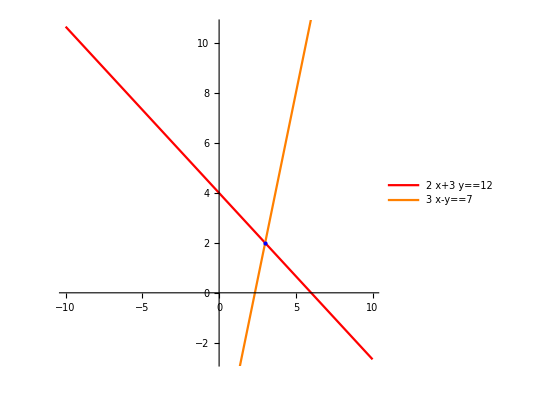
{2 x+3 y==12
3 x-y==7 | -Graphics-

```mathematica
eqs2x2 = {2x+3y==12, 3x-y== 7};

Grid[{{displayEquationSystem[eqs2x2],plotLinearSystem2[eqs2x2[[1]],eqs2x2[[2]]]}},Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],Spacings->{5,5},ItemSize->{{Scaled[0.3],Scaled[0.7]}},Alignment->Center,ItemStyle->{FontFamily->"Roboto Condensed",{FontSize->40},{1,2}->{FontSize->20}}]
```

```mathematica
backTag = "SistemiLineari";
forwardTag = "SistemiLineariPag3";
navAvantiInizioIndietro := Grid[{{backButton, backLink, startButton, startLink, forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Left, Right, Right}}, ItemSize->{{Scaled[0.05],Scaled[0.28], Scaled[0.05],Scaled[0.29],Scaled[0.28],Scaled[0.05]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbSistemiLineariHome.nb | IndietroHome.nbSistemiLineariHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbSistemiLineariPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbSistemiLineariPag3Home.nb

### Dai sistemi lineari...

#### I sistemi di equazioni di primo grado: Esempio di sistema di tre equazioni in tre incognite

Risoluzione per via grafica con intersezione dei piani.

```mathematica
eqs3x3 = {x+y+z==6,2x+y-z==1,2x-3y+z==-1};
Grid[{{displayEquationSystem[eqs3x3],plotLinearSystem3[eqs3x3[[1]],eqs3x3[[2]],eqs3x3[[3]]]}},Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],Spacings->{5,5},ItemSize->{{Scaled[0.3],Scaled[0.7]}},Alignment->Center,ItemStyle->{FontFamily->"Roboto Condensed",{FontSize->40},{1,2}->{FontSize->20}}]
```

{x+y+z==6
2 x+y-z==1
2 x-3 y+z==-1 | -Graphics3D-

```mathematica
backTag = "SistemiLineariPag2";
forwardTag = "Risoluzione";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbSistemiLineariPag2Home.nb | IndietroHome.nbSistemiLineariPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbRisoluzioneHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbRisoluzioneHome.nb

### Dai sistemi lineari...

#### Risoluzione

```mathematica
text= "Dovresti già conoscere qualche metodo per risolvere i sistemi lineari.\nProsegui al "<>ToString[Hyperlink[Button[Style["PROSSIMO CAPITOLO", FontFamily-> "Roboto Condensed", FontSize-> 24, RGBColor[0.13,0.52,0.96], Bold], Appearance-> {None}],{"Home.nb", "BlackboardHeader"}], StandardForm]<>" per scoprire un nuovo strumento di risoluzione.\nÈ un metodo generale che, come vedremo, include come casi particolari quelli che già conosci.";
Grid[{{text}}, Frame -> None, Alignment->{{Left, Right}},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left] ]
```

Dovresti già conoscere qualche metodo per risolvere i sistemi lineari.
Prosegui al PROSSIMO CAPITOLO per scoprire un nuovo strumento di risoluzione.
È un metodo generale che, come vedremo, include come casi particolari quelli che già conosci.

```mathematica
navInizio := Grid[{{startButton,startLink}},Alignment->{{Right,Left}}, ItemSize->{{Scaled[0.05],Scaled[0.95]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,5},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navInizio
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive

### ... alle Matrici

```mathematica
styledString2 = {"È possibile rappresentare un sistema lineare come una matrice, ossia una tabella ordinata i cui elementi sono:\ni coefficienti e i termini noti del sistema. Questa è detta ", Style["MATRICE COMPLETA", Red],".\nIl sistema deve essere strutturato con le ",Style[" incognite in ordine alfabetico", Bold],".\nI coefficienti devono essere inseriti all'interno della matrice mantenendo l'ordine che si presenta nel sistema.\n\nGuarda i colori per comprendere il posizionamento dei numeri!"};
styledString2 = Apply[StringJoin, ToString[#, StandardForm] &/@ styledString2 ];

Grid[{{styledString2}}, Frame -> None, ItemSize->Scaled[1], Spacings->{2,2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left]]
Spacer[5]
linearSystem1 = {7x+6y+5z==-5, 3x-4y+2z==1, -5x+6y-4z == 1};
matrixForm1=transformToMatrix[linearSystem1,True];
matrixForm1 = MapAt[Style[#,RGBColor[0.99,0.42,0]]&,matrixForm1,{{All,1}}];
matrixForm1 = MapAt[Style[#,RGBColor[0.6,0.2,1]]&,matrixForm1,{{All,2}}];
matrixForm1 = MapAt[Style[#,RGBColor[0.99,0.47,1]]&,matrixForm1,{{All,3}}];
matrixForm1 = MapAt[Style[#,RGBColor[0.14,0.62,0.14]]&,matrixForm1,{{All,4}}];

linearSystem2= {7x+6y+5z==0,-4y+2z ==1,5x+6y==1};
matrixForm2 = transformToMatrix[linearSystem2,True];
matrixForm2 = MapAt[Style[#,RGBColor[0.99,0.42,0]]&,matrixForm2,{{All,1}}];
matrixForm2 = MapAt[Style[#,RGBColor[0.6,0.2,1]]&,matrixForm2,{{All,2}}];
matrixForm2 = MapAt[Style[#,RGBColor[0.99,0.47,1]]&,matrixForm2,{{All,3}}];
matrixForm2 = MapAt[Style[#,RGBColor[0.14,0.62,0.14]]&,matrixForm2,{{All,4}}];

Grid[{{Image[Import["images/sistemaColorato1.png"],Magnification->0.5],"⟹",matrixForm1//MatrixForm},{Image[Import["images/sistemaColorato2.png"],Magnification->0.5],"⟹",matrixForm2//MatrixForm}},Frame -> None, ItemSize->Fit, Spacings->{1, 2}, ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center],Alignment->{{Right, Center, Left}}]
Spacer[20]
```

È possibile rappresentare un sistema lineare come una matrice, ossia una tabella ordinata i cui elementi sono:
i coefficienti e i termini noti del sistema. Questa è detta MATRICE COMPLETA.
Il sistema deve essere strutturato con le  incognite in ordine alfabetico.
I coefficienti devono essere inseriti all'interno della matrice mantenendo l'ordine che si presenta nel sistema.

Guarda i colori per comprendere il posizionamento dei numeri!

-Graphics- | ⟹ | (7 | 6 | 5 | -5
3 | -4 | 2 | 1
-5 | 6 | -4 | 1)
-Graphics- | ⟹ | (7 | 6 | 5 | 0
0 | -4 | 2 | 1
5 | 6 | 0 | 1)

#### Attenzione ! Se nel sistema non compare un’incognita, nella matrice al posto corrispondente bisogna mettere uno 0 (zero).

```mathematica
forwardTag = "MatriciPag2";
exerciseTag = "ProvaTuSistemaMatrice";
exerciseButton := Hyperlink[Button[Image[Import["images/copybook.png"]], Appearance->{None}, ImageSize->{60,60}],{"Home.nb", exerciseTag}];
exerciseLink := Hyperlink["Prova tu!", {"Home.nb", exerciseTag},BaseStyle->RGBColor[0.2,0.6,0.86]];
navAvantiInizioEsercizio := Grid[{{startButton,startLink,exerciseButton, exerciseLink, forwardLink,forwardButton}},Alignment->{{Right, Left,Right,Left, Right, Left}}, ItemSize->{{Scaled[0.05],Scaled[0.28],Scaled[0.05],Scaled[0.29],Scaled[0.28],Scaled[0.05]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiInizioEsercizio
Clear[forwardTag];
Clear[exerciseTag];
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuSistemaMatriceHome.nb | Prova tu!Home.nbProvaTuSistemaMatriceHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag2Home.nb

### Matrici

#### Definizione di matrice

```mathematica
matrixElement = Subscript[a, HoldForm["i""j"]];
matrix ={{Subscript[a, HoldForm["1"1]], Subscript[a, HoldForm["1"2]], …, Subscript[a, HoldForm["1""m"]]}, {Subscript[a, HoldForm["2"1]], Subscript[a, HoldForm["2"2]], …, Subscript[a, HoldForm["2""m"]]}, {⋮, ⋮, ⋱, ⋮}, {Subscript[a, HoldForm["n"1]], Subscript[a, HoldForm["n"2]], …, Subscript[a, HoldForm["n""m"]]}} // MatrixForm;matrixRule = <| "1"-> Style[matrix[[1,1,1,2,1]], RGBColor[0.13,0.52,0.96]], 1-> Style[matrix[[1,1,1,2,1]], Red], 2 -> Style[matrix[[1,2,1,2,1]], Red], "2" -> Style[matrix[[1,2,1,2,1]],RGBColor[0.13,0.52,0.96]], "m" -> Style[matrix[[1,1,4,2,1,2]], Red], "n" -> Style[matrix[[1,4,1,2,1]], RGBColor[0.13,0.52,0.96]]|>;
matrixElementRule = <| "i" ->  Style[matrixElement[[2,1,1]], RGBColor[0.13,0.52,0.96]], "j" -> Style[matrixElement[[2,1,2]], Red]|>;
myMatrix = matrix /. matrixRule;
myMatrixElement = matrixElement /. matrixElementRule;
stringMatrix = {"matrice ", Style["n", RGBColor[0.13,0.52,0.96]], " x ",  Style["m", Red]};
stringMatrix = Apply[StringJoin, ToString[#, StandardForm]& /@ stringMatrix];
columns = Image[Import["images/cols.png"],Magnification->0.7];
rows = Image[Import["images/rows.png"],Magnification->0.7];
Grid[{{"Una matrice è una tabella ordinata di elementi disposti su " <> ToString[Style["n", RGBColor[0.13,0.52,0.96]],StandardForm] <> " righe e " <> ToString[Style["m", Red],StandardForm] <> " colonne."},{
Grid[{{myMatrixElement,columns},{rows,myMatrix},{stringMatrix,SpanFromLeft}},Frame->None, Spacings->{1,1}]
}}, ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->28], ItemSize->Fit, Frame->None,Spacings->{0,2}]
Spacer[15]
Grid[{{"Al suo interno possono comparire numeri positivi, negativi o anche zeri."}},Frame -> None, ItemSize->Scaled[1], Spacings->{2, 2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->28, TextAlignment->Center]]
```

Una matrice è una tabella ordinata di elementi disposti su n righe e m colonne.
a_(i j) | -Graphics-
-Graphics- | (a_(1 1) | a_(1 2) | … | a_(1 m)
a_(2 1) | a_(2 2) | … | a_(2 m)
⋮ | ⋮ | ⋱ | ⋮
a_(n 1) | a_(n 2) | … | a_(n m))
matrice n x m |

Al suo interno possono comparire numeri positivi, negativi o anche zeri.

```mathematica
backTag = "MatriciPag1";
forwardTag = "MatriciPag3";
navAvantiInizioIndietro
Clear[backTag, forwardTag];
```

-Graphics-Home.nbMatriciPag1Home.nb | IndietroHome.nbMatriciPag1Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag3Home.nb

### Matrici

#### Elemento di una matrice

```mathematica
matrixPhrase="Un elemento è individuato univocamente da due indici ordinati: il numero di riga e il numero di colonna.";

tableMatrix =Grid[
Table[
{
{"", Rotate[" 1.aa Colonna", Pi/2],Rotate[" 2.aa Colonna", Pi/2],Rotate[" 3.aa Colonna", Pi/2],Rotate[" 4.aa Colonna", Pi/2]},
{"R1: 1.aa riga",7,6,5,0},
{"R2: 2.aa riga",0,-4,2,1},
{"R3: 3.aa riga",5,Item[7, Frame-> True, FrameStyle->Directive[Yellow, Thickness-> Large]],0,1}}
],
Dividers->{{None,Black,None,None,None,Black},{None, Black, None, None, Black}}, Background->{Automatic,Automatic,{{{4,4},{2,5}}->Red,{{2,4},{3,3}}->Blue}}, ItemStyle->{Automatic,Automatic,{{2,4},{3,3}}->{FontColor->White}}];
exampleImage = -Graphics-;
Grid[{{matrixPhrase},{tableMatrix}, {exampleImage}}, Frame -> None, ItemSize->Scaled[1], Spacings->{3, 3},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center]]
```

Un elemento è individuato univocamente da due indici ordinati: il numero di riga e il numero di colonna.
 |  1.aa Colonna |  2.aa Colonna |  3.aa Colonna |  4.aa Colonna
R1: 1.aa riga | 7 | 6 | 5 | 0
R2: 2.aa riga | 0 | -4 | 2 | 1
R3: 3.aa riga | 5 | 7 | 0 | 1
-Graphics-

```mathematica
backTag = "MatriciPag2";
forwardTag = "MatriciPag4";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag2Home.nb | IndietroHome.nbMatriciPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag4Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag4Home.nb

### Matrici

#### Tipologia di matrici

```mathematica
firstStringSquaredMatrix = {Style["Matrice quadrata\n", Bold], "numero di righe = numero di colonne"};
firstStringSquaredMatrix = Apply[StringJoin, ToString[#, StandardForm] & /@ firstStringSquaredMatrix];
firstStringRectangularMatrix = {Style["Matrice rettangolare\n", Bold], Style["numero di righe ≠ numero di colonne", FontFamily-> "Roboto Condensed", FontSize-> 24]};
firstStringRectangularMatrix = Apply[StringJoin, ToString[#, StandardForm] & /@ firstStringRectangularMatrix];
squaredMatrix = {{4, 3, 7, 9, -1}, {7, 1, 0, 6, 5}, {1, 6, 3, -4, 5}, {0, -7, 0, -9, 2}, {5, -1, -1, 7, 0}} // MatrixForm;
rectangularMatrix = {{7, 6, 5, 0}, {0, -4, 2, 1}, {5, 7, 0, 1}} // MatrixForm;
secondStringSquaredMatrix = Style["Matrice 5 x 5", Italic];
secondStringRectangularMatrix = Style["Matrice 3 x 4", Italic];

Grid[{{firstStringSquaredMatrix,firstStringRectangularMatrix}, {squaredMatrix, rectangularMatrix}, {secondStringSquaredMatrix, secondStringRectangularMatrix}}, Frame-> None, Spacings-> {1,1}, ItemSize-> Fit ,ItemStyle-> Directive[TextAlignment -> Center, FontFamily -> "Roboto Condensed", FontSize -> 24]]
```

Matrice quadrata
numero di righe = numero di colonne | Matrice rettangolare
numero di righe ≠ numero di colonne
(4 | 3 | 7 | 9 | -1
7 | 1 | 0 | 6 | 5
1 | 6 | 3 | -4 | 5
0 | -7 | 0 | -9 | 2
5 | -1 | -1 | 7 | 0) | (7 | 6 | 5 | 0
0 | -4 | 2 | 1
5 | 7 | 0 | 1)
Matrice 5 x 5 | Matrice 3 x 4

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag3"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag5"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag3";
forwardTag = "MatriciPag5";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag3Home.nb | IndietroHome.nbMatriciPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag5Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag5Home.nb

### Matrici

#### Diagonale di una matrice

```mathematica
firstString = "La " <> ToString[Style["diagonale", Bold], StandardForm] <> " di una matrice quadrata è composta dai numeri che hanno indice di riga uguale a indice di colonna.\nSono quelli evidenziati in " <> ToString[Style["rosso", Red], StandardForm] <> ".";
secondString = {Style["Attenzione!\n", Red, Bold], "Non esiste la diagonale di una matrice rettangolare, tuttavia nelle matrici complete che tratteremo ci sarà utile un concetto simile per riconoscere elementi particolari."};
secondString = Apply[StringJoin, ToString[#, StandardForm] & /@ secondString];

squaredMatrix = {{Style[7, Red], 6, 5}, {0, Style[-4, Red], 2}, {5, 7, Style[0, Red]}}  // MatrixForm;
rectangularMatrix = {{Style[7, RGBColor[0.2, 0.6, 0.2]], 6, 5, 0}, {0, Style[-4, RGBColor[0.2, 0.6, 0.2]], 2, 1}, {5, 7, Style[3, RGBColor[0.2, 0.6, 0.2]], 1}} // MatrixForm;

Grid[{{firstString}, {squaredMatrix}, {secondString}, {rectangularMatrix}}, Frame -> None, Spacings-> {0,2}, ItemSize-> Fit, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, TextAlignment -> Center]]
```

La diagonale di una matrice quadrata è composta dai numeri che hanno indice di riga uguale a indice di colonna.
Sono quelli evidenziati in rosso.
(7 | 6 | 5
0 | -4 | 2
5 | 7 | 0)
Attenzione!
Non esiste la diagonale di una matrice rettangolare, tuttavia nelle matrici complete che tratteremo ci sarà utile un concetto simile per riconoscere elementi particolari.
(7 | 6 | 5 | 0
0 | -4 | 2 | 1
5 | 7 | 3 | 1)

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag4"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag6"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag4";
forwardTag = "MatriciPag6";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag4Home.nb | IndietroHome.nbMatriciPag4Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag6Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag6Home.nb

### Matrici

#### Matrice triangolare e a gradini

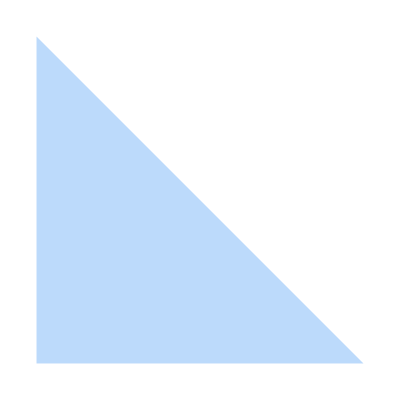
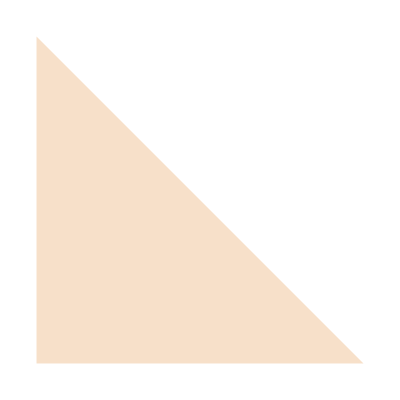
Una matrice quadrata che presenta tutti elementi uguali a zero sotto la diagonale prende il nome di matrice triangolare superiore.
-Graphics-(7 | 6 | 5
0 | -4 | 2
0 | 0 | 9)
Una matrice rettangolare a gradini presenta tutti elementi uguali a zero sotto i numeri evidenziati in verde che chiameremo pivot.
-Graphics-(7 | 6 | 5 | 0
0 | -4 | 2 | 1
0 | 0 | 3 | 1)

```mathematica
firstString = {"Una matrice quadrata che presenta tutti elementi uguali a zero sotto la diagonale prende il nome di ", Style["matrice triangolare superiore", Bold], "."};
firstString= Apply[StringJoin, ToString[#, StandardForm] & /@ firstString];
secondString = {"Una ", Style["matrice rettangolare a gradini", Bold], " presenta tutti elementi uguali a zero sotto i numeri evidenziati in verde che chiameremo ", Style["pivot",  RGBColor[0.2, 0.6, 0.2], Bold], "."};
secondString = Apply[StringJoin, ToString[#, StandardForm] & /@ secondString];

squaredMatrix = {{Style[7, Red], 6, 5}, {0, Style[-4, Red], 2}, {0, 0, Style[9, Red]}}  // MatrixForm;
rectangularMatrix = {{Style[7, RGBColor[0.2, 0.6, 0.2]], 6, 5, 0}, {0, Style[-4, RGBColor[0.2, 0.6, 0.2]], 2, 1}, {0, 0, Style[3, RGBColor[0.2, 0.6, 0.2]], 1}} // MatrixForm;

triangle = Triangle[{{0,0}, {0,1}, {1,0}}];
triangleGridSquaredMatrix = Grid[{{Graphics[{RGBColor[0.13,0.52,0.96, 0.3], triangle}]}}, ItemSize-> 4.5, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings -> {0.5,1}];
triangleGridRectagularMatrix = Grid[{{Graphics[{RGBColor[0.9,0.60,0.30, 0.3], triangle}]}}, ItemSize-> 4.5, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings -> {0.5,1}];
upperTriangularMatrix = Overlay[{triangleGridSquaredMatrix, squaredMatrix},All, 2];
rectangularSteppedMatrix = Overlay[{triangleGridRectagularMatrix, rectangularMatrix},All, 2];

Grid[{{firstString}, {upperTriangularMatrix}, {secondString}, {rectangularSteppedMatrix}}, Frame -> None, ItemSize-> Fit, Spacings-> {0,2}, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, TextAlignment -> Center]]
```

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag5"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag7"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag5";
forwardTag = "MatriciPag7";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag5Home.nb | IndietroHome.nbMatriciPag5Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag7Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag7Home.nb

### Matrici

#### Matrice diagonale e matrice identità

```mathematica
firstString = {"Una matrice quadrata che presenta elementi diversi da zero solo sulla diagonale si chiama ", Style["matrice diagonale", Bold],"."};
firstString= Apply[StringJoin, ToString[#, StandardForm] & /@ firstString];
secondString = {"La matrice diagonale che presenta solo 1 sulla diagonale si chiama ", Style["matrice identità", Bold],"."};
secondString = Apply[StringJoin, ToString[#, StandardForm] & /@ secondString];

diagonalMatrix = {{Style[7, Red], 0, 0}, {0, Style[-4, Red], 0}, {0, 0, Style[9, Red]}} // MatrixForm;
identityMatrix = {{Style[1, Red], 0, 0}, {0, Style[1, Red], 0}, {0, 0, Style[1, Red]}} // MatrixForm;

Grid[{{firstString}, {diagonalMatrix}, {secondString}, {identityMatrix}}, Frame-> None, ItemSize-> Fit, Spacings-> {0,2}, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, TextAlignment -> Center]]
```

Una matrice quadrata che presenta elementi diversi da zero solo sulla diagonale si chiama matrice diagonale.
(7 | 0 | 0
0 | -4 | 0
0 | 0 | 9)
La matrice diagonale che presenta solo 1 sulla diagonale si chiama matrice identità.
(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
backTag = "MatriciPag6";
navIndietroInizio := Grid[{{backButton, backLink, startLink, startButton}},Alignment->{{Right, Left, Right, Left}}, ItemSize->{{Scaled[0.05],Scaled[0.45],Scaled[0.45],Scaled[0.05]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navIndietroInizio
Clear[backTag];
```

-Graphics-Home.nbMatriciPag6Home.nb | IndietroHome.nbMatriciPag6Home.nbHyperlinkHyperlinkActive | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb

### Metodo di Gauss

Il metodo di Gauss è un procedimento ordinato di calcolo che permette la risoluzione di un sistema lineare
mediante un numero finito di step attraverso l'uso di matrici.

Lo scopo è quello di ridurre a gradini la matrice completa associata al sistema.

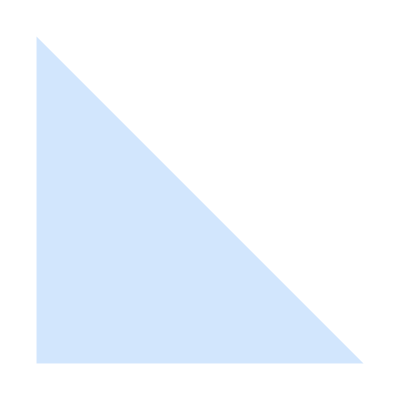
{a+b+4 c-d==9
a-c==1
a-2 b+4 c==6
2 a+3 c-3 d==8 | ⟶ | (1 | 1 | 4 | -1 | 9
1 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
2 | 0 | 3 | -3 | 8) | ⟶ | -Graphics-(2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | 15/4 | 5/4 | 6
0 | 0 | 0 | 7/3 | 1)
Sistema lineare |  | Matrice completa associata |  | Matrice ridotta a gradini

Come ottenere gli zeri che vedi nella matrice ridotta a gradini?

```mathematica
gaussFirstString = {"Il metodo di Gauss è un procedimento ordinato di calcolo che permette la risoluzione di un sistema lineare\nmediante un numero finito di ", Style["step", Bold, FontSize-> 30]," attraverso l'uso di ", Style["matrici", Bold, FontSize-> 30],"."};
gaussFirstString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussFirstString ];
gaussThirdString = {"\nLo scopo è quello di ", Style["ridurre a gradini", Bold], " la matrice completa associata al sistema."};
gaussThirdString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussThirdString ];

linearSystem = {a+b+4c-d== 9, a-c== 1, a-2b+4c== 6, 2a+3c-3d== 8};
transformed = transformToMatrix[linearSystem, True];
matrix = highlightMatrixElements[transformed] // MatrixForm;
{L,U,P,newB}=fattorizzazioneLU[Drop[transformed,None,-1],Take[transformed,All,-1]];
upperMatrix = highlightMatrixElements[Join[U,ArrayReshape[newB,{Length[newB],1}],2]]//MatrixForm;
triangle = Triangle[{{0,0}, {0,4}, {4,0}}];
triangleMatrix = Grid[{{Graphics[{RGBColor[0.13,0.52,0.96, 0.2], triangle}]}}, ItemSize-> 7, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings -> {0.5,2}];
upperMatrix = Overlay[{triangleMatrix, upperMatrix}, All, 2];

thirdString = Style["Sistema lineare", Italic];
fourthString = Style["Matrice completa associata", Italic];
fifthString = Style["Matrice ridotta a gradini", Italic];

Grid[{{gaussFirstString}, {gaussThirdString}}, Frame -> None,ItemSize-> Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left]
Framed[Grid[{{Grid[{{displayEquationSystem[linearSystem], "⟶", matrix, "⟶", upperMatrix}, {thirdString, "",fourthString, "",fifthString}}, Frame -> None,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Spacings->{5,0}]}}, Frame->None, ItemSize->Fit], FrameStyle-> None, FrameMargins-> {{0,0}, {0,30}}]
Framed[Grid[{{"Come ottenere gli zeri che vedi nella matrice ridotta a gradini?"}}, Frame -> True, FrameStyle-> RGBColor[0.94,0.94,0.94],Background->RGBColor[1,0.8,0.4], ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24]], 
FrameStyle-> None, FrameMargins-> {{0,0}, {0,30}}]
```

```mathematica
forwardTag = "GaussPag2";
navAvantiInizio
Clear[forwardTag];
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag2Home.nb

### Metodo di Gauss

#### Le mosse

```mathematica
gaussFirstString = {"Ogni step può essere composto da una o più ", Style["«mosse»", Bold], " tra le seguenti:"};
gaussFirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ gaussFirstString ];
gaussSecondString = {"• ",Style["MOSSA 1", Bold],": scambio di due righe della matrice."};
gaussSecondString = Apply[StringJoin, ToString[#, StandardForm] & /@ gaussSecondString ];
gaussThirdString = {"• ", Style["MOSSA 2", Bold],": combinazione (lineare) di righe:\n  ",Style["Sostituire una riga della matrice con un’altra, ottenuta sottraendo ad essa\n  un’altra riga moltiplicata precedentemente per un numero diverso da zero.", FontSize->21]};
gaussThirdString = Apply[StringJoin, ToString[#, StandardForm] & /@ gaussThirdString ];

lookHerePlay1 = Hyperlink["Guarda qui", {"Home.nb", "GaussPag3"}, BaseStyle -> RGBColor[0.2, 0.6, 0.86]];
lookHerePlay2 = Hyperlink["Guarda qui", {"Home.nb", "GaussPag4"}, BaseStyle -> RGBColor[0.2, 0.6, 0.86]];
lookHerePlay1Grid = Grid[{{lookHerePlay1}}, Frame -> None, ItemStyle -> Directive[FontFamily -> "Roboto Condensed", FontSize -> 30, FontWeight -> Bold]];
lookHerePlay2Grid = Grid[{{lookHerePlay2}}, Frame -> None, ItemStyle -> Directive[FontFamily -> "Roboto Condensed", FontSize -> 30, FontWeight -> Bold]];

Grid[{{gaussFirstString}, {Framed[Grid[{{gaussSecondString , lookHerePlay1Grid}, {gaussThirdString, lookHerePlay2Grid}}, Frame -> None, Alignment -> {Left, Bottom}, Spacings -> {2, 1}], FrameStyle -> None, FrameMargins -> {{30, 0}, {0, 0}}]}}, Frame -> None, ItemStyle -> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment -> Left]
```

Ogni step può essere composto da una o più «mosse» tra le seguenti:
• MOSSA 1: scambio di due righe della matrice. | Guarda quiHome.nbGaussPag3Home.nbHyperlinkHyperlinkActive
• MOSSA 2: combinazione (lineare) di righe:
  Sostituire una riga della matrice con un’altra, ottenuta sottraendo ad essa
  un’altra riga moltiplicata precedentemente per un numero diverso da zero. | Guarda quiHome.nbGaussPag4Home.nbHyperlinkHyperlinkActive

```mathematica
backTag = "GaussPag1";
forwardTag = "GaussPag3";
navAvantiInizioIndietro
Clear[backTag, forwardTag];
```

-Graphics-Home.nbGaussPag1Home.nb | IndietroHome.nbGaussPag1Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag3Home.nb

### Metodo di Gauss

#### Mossa 1

```mathematica
myString1 = "Scambio di due righe della matrice:";
firstMatrix = {{1,4,0,6},{2,6,2,8},{0,3,-3,8}};
firstMatrix = MapAt[Style[#,Red]&,firstMatrix,{1,All}];
firstMatrix = MapAt[Style[#,RGBColor[1,0,1]]&,firstMatrix,{2,All}];
secondMatrix = Permute[firstMatrix, {2,1}]//MatrixForm;
firstMatrix = firstMatrix//MatrixForm;
(*firstMatrix = {{Style[1, Red],Style[4, Red],Style[0, Red],Style[6, Red]}, {Style[2, RGBColor[1,0,1]],Style[6, RGBColor[1,0,1]],Style[2, RGBColor[1,0,1]],Style[8, RGBColor[1,0,1]]}, {0,3,-3,8}} // MatrixForm;
secondMatrix = {{Style[2, RGBColor[1,0,1]],Style[6, RGBColor[1,0,1]],Style[2, RGBColor[1,0,1]],Style[8, RGBColor[1,0,1]]}, {Style[1, Red],Style[4, Red],Style[0, Red],Style[6, Red]},{0,3,-3,8}} // MatrixForm;*)
leftArrow = ImageResize[-Graphics-, 30];
rightArrow =ImageResize[-Graphics-, 30];
Grid[{{myString1}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
matrixGrid = Grid[{{leftArrow, firstMatrix, rightArrow}}, Frame-> None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Top];
rowsGrid = Grid[{{"R2 ↔ R1"}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94], ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, FontWeight-> Bold], Background-> RGBColor[0.13,0.52,0.96, 0.5]];
Grid[{{Grid[{{matrixGrid, rowsGrid, secondMatrix}}, Frame-> True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Spacings-> {10,5}]}}, Frame->None, ItemSize->Fit]

myString = {"Ogni elemento della riga 2 (", Style["R2", Bold],") adesso è sulla riga 1 (", Style["R1", Bold],") e viceversa."};
myString = Apply[StringJoin, ToString[#, StandardForm] &/@ myString ];
Grid[{{myString}}, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
```

Scambio di due righe della matrice:

-Graphics- | (1 | 4 | 0 | 6
2 | 6 | 2 | 8
0 | 3 | -3 | 8) | -Graphics- | R2 ↔ R1 | (2 | 6 | 2 | 8
1 | 4 | 0 | 6
0 | 3 | -3 | 8)

Ogni elemento della riga 2 (R2) adesso è sulla riga 1 (R1) e viceversa.

```mathematica
backTag = "GaussPag2";
forwardTag = "GaussPag4";
navAvantiInizioIndietro
Clear[backTag, forwardTag];
```

-Graphics-Home.nbGaussPag2Home.nb | IndietroHome.nbGaussPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag4Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag4Home.nb

### Metodo di Gauss

#### Mossa 2

```mathematica
firstString = {"Sostituire una riga (",Style["R2",Bold],") della matrice con un’altra (",Style["nuova R2", Bold],"), ottenuta ",Style["sottraendo", Underlined] ," ad essa (",Style["R2",Bold],") un’altra riga (",Style["R1",Bold],") moltiplicata\nprecedentemente per un ",Style["numero diverso da zero", Bold,Red],".\n",Style["L’obiettivo è quello di ottenere degli zeri", Underlined],".\nEsempio: Vogliamo annullare l’elemento ",Framed[" 1 ", RoundingRadius-> 100, FrameStyle-> Orange]," sotto il pivot ", Style[3, Bold, RGBColor[0.2, 0.6, 0.2]],"."};
firstString = Apply[StringJoin, ToString[#, StandardForm] &/@ firstString ];

rowSubstitution = ImageResize[-Graphics-, 600];
firstMatrix = {{Style[3, Bold, RGBColor[0.2, 0.6, 0.2]],6,-2,9}, {Framed[" 1 ", RoundingRadius->100, FrameStyle->Orange],4,0,6}, {0,3,-3,8}} // MatrixForm;
secondMatrix = {{3,6,-2,9}, {1-HoldForm[3/3], 4-HoldForm[6/3], HoldForm[0] -HoldForm[-2/3]"", 6-HoldForm[9/3]}, {0,3,-3,8}} // MatrixForm;
thirdMatrix = {{Style[3, Bold, RGBColor[0.2, 0.6, 0.2]],6,-2,9}, {Framed[" 0 ", RoundingRadius->100, FrameStyle->Orange],3,2/3,3}, {0,3,-3,8}} // MatrixForm;

secondString = {"Il ", Style["numero diverso da zero", Bold,Red], " sarà: ", HoldForm[Style["elemento da annullare",Italic, FontSize->24]/Style["pivot",Italic, FontSize->24]]};
secondString = Apply[StringJoin, ToString[#, StandardForm] &/@ secondString ];

Grid[{{firstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
Grid[{{rowSubstitution}, {Grid[{{firstMatrix, "⟶", secondMatrix, "⟶", thirdMatrix}},Frame->None, Spacings->{3,0}]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Spacings->{0,4}] /. x_Image:>Image[x,Magnification->1]
Grid[{{secondString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
```

Sostituire una riga (R2) della matrice con un’altra (nuova R2), ottenuta sottraendo ad essa (R2) un’altra riga (R1) moltiplicata
precedentemente per un numero diverso da zero.
L’obiettivo è quello di ottenere degli zeri.
Esempio: Vogliamo annullare l’elemento  1  sotto il pivot 3.

-Graphics-
(3 | 6 | -2 | 9
 1  | 4 | 0 | 6
0 | 3 | -3 | 8) | ⟶ | (3 | 6 | -2 | 9
1-3/3 | 4-6/3 | 0- (-2/3) | 6-9/3
0 | 3 | -3 | 8) | ⟶ | (3 | 6 | -2 | 9
 0  | 3 | 2/3 | 3
0 | 3 | -3 | 8)

Il numero diverso da zero sarà: (elemento da annullare)/pivot

```mathematica
backTag = "GaussPag3";
forwardTag = "GaussPag5";
navAvantiInizioIndietro
Clear[backTag, forwardTag];
```

-Graphics-Home.nbGaussPag3Home.nb | IndietroHome.nbGaussPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag5Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag5Home.nb

### Metodo di Gauss

#### Step 1 • Colonna 1

È necessario operare sulla matrice con la MOSSA 1 dello scambio di righe
in modo da scegliere come pivot l’elemento massimo in valore assoluto.
Ad esempio:

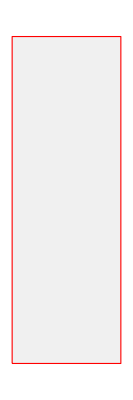
-Graphics-(1 | 1 | 4 | -1 | 9
1 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
 2  | 0 | 3 | -3 | 8) | • Cerca per la prima colonna l'elemento massimo.
  E' il  2  in posizione a_41.

Nota bene:
Il pivot non deve essere mai zero.
Se ci sono due pivot uguali in valore assoluto devi scegliere il primo che trovi scorrendo dall'alto verso il basso.

```mathematica
gaussFirstString = {"È necessario operare sulla matrice con la ", Style["MOSSA 1", Bold]," dello ", Style["scambio di righe", Bold], "\nin modo da scegliere come ", Style["pivot ", Bold, RGBColor[0.2, 0.6, 0.2]],Style["l’elemento massimo in valore assoluto", Bold, Underlined],".\nAd esempio:"};
gaussFirstString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussFirstString ];
gaussSecondString = {"• Cerca per la prima colonna l'elemento massimo.\n  E' il ", Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_41."};
gaussSecondString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussSecondString ];
thirdString = Style["Nota bene:", Bold, Red];
fourthString = {"Il pivot non deve essere mai zero.\nSe ci sono due pivot uguali in valore assoluto devi scegliere il " ,Style["primo", Bold, Underlined]," che trovi scorrendo dall'alto verso il basso."};
fourthString = Apply[StringJoin, ToString[#, StandardForm] &/@ fourthString ];

matrix = {{1,1,4,-1,9}, {1,0,-1,0,1}, {1,-2,4,0,6}, {Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange],0,3,-3,8}} // MatrixForm;
rectangle = Rectangle[{0,0},{0.5,1.5}];
rectangleMatrix = Grid[{{Graphics[{EdgeForm[{Thick, Red}],RGBColor[0.94, 0.94, 0.94], rectangle}]}}, ItemSize->3, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings-> {0.6,0}];
designedMatrix = Overlay[{rectangleMatrix, Framed[matrix, FrameStyle-> None, FrameMargins->{{0,0}, {0,8}}]}, All, 2];

Grid[{{gaussFirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left]
Grid[{{designedMatrix, gaussSecondString}}, Frame->True,FrameStyle -> RGBColor[0.94,0.94,0.94],ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}, Spacings->{0,5}]
Grid[{{thirdString}, {fourthString}}, Frame->None,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
```

```mathematica
backTag = "GaussPag4";
forwardTag = "GaussPag6";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti := Grid[{{backButton, backLink, startButton, startLink, exerciseButton, exerciseLink,forwardLink,forwardButton}},Alignment->{{Right, Left, Right, Left,Right, Left, Right, Left}}, ItemSize->{{Scaled[0.05],Scaled[0.22], Scaled[0.05],Scaled[0.22],Scaled[0.05],Scaled[0.22],Scaled[0.14],Scaled[0.05]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navIndietroInizioEserciziAvanti
Clear[backTag,forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag4Home.nb | IndietroHome.nbGaussPag4Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag6Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag6Home.nb

### Metodo di Gauss

#### Step 1 • Colonna 1

```mathematica
gaussFirstString = {"È necessario operare sulla matrice con la " ,Style["MOSSA 1", Bold]," dello ", Style["scambio di righe", Bold], "\nin modo da scegliere come ", Style["pivot ", Bold, RGBColor[0.2, 0.6, 0.2]],Style["l’elemento massimo in valore assoluto", Bold, Underlined],".\nAd esempio:"};
gaussFirstString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussFirstString ];
gaussSecondString = {"• Cerca per la prima colonna l'elemento massimo.\n  E' il ", Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_41.\n• Scambia la prima riga con la quarta.\n  In modo da ottenere ", Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_11."};
gaussSecondString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussSecondString ];
leftArrow = ImageResize[-Graphics-, {60,150}];
rightArrow =ImageResize[-Graphics-, {60,150}];
swapRows  = ImageResize[-Graphics-, 400];
matrix = {{1,1,4,-1,9}, {1,0,-1,0,1}, {1,-2,4,0,6}, {Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange],0,3,-3,8}} // MatrixForm;
rectangle = Rectangle[{0,0},{0.5,1.5}];
rectangleMatrix = Grid[{{Graphics[{EdgeForm[{Thick, Red}],RGBColor[0.94, 0.94, 0.94], rectangle}]}}, ItemSize->3, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings-> {0.6,0}];
designedMatrix = Overlay[{rectangleMatrix, Framed[matrix, FrameStyle-> None, FrameMargins->{{0,0}, {0,8}}]}, All, 2];

Grid[{{gaussFirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left]
Grid[{{Grid[{{leftArrow, designedMatrix, rightArrow}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Top], gaussSecondString},{"", swapRows}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94], ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}, Spacings->{0,4}]
```

È necessario operare sulla matrice con la MOSSA 1 dello scambio di righe
in modo da scegliere come pivot l’elemento massimo in valore assoluto.
Ad esempio:

-Graphics- | -Graphics-(1 | 1 | 4 | -1 | 9
1 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
 2  | 0 | 3 | -3 | 8) | -Graphics- | • Cerca per la prima colonna l'elemento massimo.
  E' il  2  in posizione a_41.
• Scambia la prima riga con la quarta.
  In modo da ottenere  2  in posizione a_11.
 | -Graphics-

```mathematica
backTag = "GaussPag5";
forwardTag = "GaussPag7";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag5Home.nb | IndietroHome.nbGaussPag5Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag7Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag7Home.nb

### Metodo di Gauss

#### Step 1 • Colonna 1

```mathematica
gaussFirstString = {"È necessario operare sulla matrice con la " ,Style["MOSSA 1", Bold]," dello ", Style["scambio di righe", Bold], "\nin modo da scegliere come ", Style["pivot ", Bold, RGBColor[0.2, 0.6, 0.2]],Style["l’elemento massimo in valore assoluto", Bold, Underlined],".\nAd esempio:"};
gaussFirstString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussFirstString ];

matrix = {{Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange],0,3,-3,8},{1,0,-1,0,1}, {1,-2,4,0,6}, {1,1,4,-1,9}} // MatrixForm;
designedMatrix = Overlay[{rectangleMatrix, Framed[matrix, FrameStyle-> None, FrameMargins->{{0,0}, {0,8}}]}, All, 2];

Grid[{{gaussFirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left]
Grid[{{designedMatrix, gaussSecondString}, {"", swapRows}}, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94],ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}, Spacings->{0,4}]
```

È necessario operare sulla matrice con la MOSSA 1 dello scambio di righe
in modo da scegliere come pivot l’elemento massimo in valore assoluto.
Ad esempio:

-Graphics-( 2  | 0 | 3 | -3 | 8
1 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
1 | 1 | 4 | -1 | 9) | • Cerca per la prima colonna l'elemento massimo.
  E' il  2  in posizione a_41.
• Scambia la prima riga con la quarta.
  In modo da ottenere  2  in posizione a_11.
 | -Graphics-

```mathematica
backTag = "GaussPag6";
forwardTag = "GaussPag8";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag6Home.nb | IndietroHome.nbGaussPag6Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag8Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag8Home.nb

### Metodo di Gauss

#### Step 2 • Colonna 1, Riga 2

```mathematica
normalOne = Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24];
pivotTwo = Style[2, Bold,RGBColor[0.2,0.6,0.2], FontFamily->"Roboto Condensed",FontSize->24];
step2FirstString = {"Rendere nullo il ", Style["primo elemento", Orange] ," sotto il ",Style["pivot a_11 = 2", Bold , RGBColor[0.2, 0.6, 0.2]]," ed effettuare la ",Style["MOSSA 2", Bold]," per ",Style["tutti", Bold,Underlined], " gli elementi della ",Style["stessa", Bold] ," riga."};
step2FirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ step2FirstString];
step3SecondString = {Style["MOSSA 2",Bold],"\nnuova R_2 : R_2 - ",normalOne/pivotTwo," R_1"};
step3SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step3SecondString];

matrixStep2 = {{2,0,3,-3,8},{0,0,-1,0,1}, {1,-2,4,0,6}, {1,1,4,-1,9}};
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,matrixStep2,{{Range[1,2],Range[2,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{Range[3,4],Range[1,5]}}];
finalMatrixStep2 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2]]&,finalMatrixStep2,{{1,1}}];
finalMatrixStep2 = MapAt[Framed[#, FrameStyle->Orange]&,finalMatrixStep2,{{2,1}}];
finalMatrixStep2 = finalMatrixStep2 // MatrixForm;

red1 = Style[0, Red];
blue1 = Style[-1, Blue];
blue2 = Style[3, Blue];
purple2= Style[-3, RGBColor[1,0,1]];
purple1 = Style[0, RGBColor[1,0,1]];
lightBlue2 = Style[8, RGBColor[0.13,0.52,0.96]];
lightBlue1 = Style[-3,RGBColor[0.13,0.52,0.96]];

firstOperation = {"0 - ", normalOne /pivotTwo," × 0 = ", red1};
firstOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ firstOperation];
secondOperation = {"-1 - ",normalOne/pivotTwo," × 3 = ",Style["-",Blue],Style[5, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]};
secondOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ secondOperation];
thirdOperation = {"0 - ",normalOne/pivotTwo," × (-3) = ",Style[3, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]};
thirdOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ thirdOperation];
fourthOperation = {"1 - ",normalOne/pivotTwo," × 8 = ",lightBlue1};
fourthOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ fourthOperation];
fifthOperation = {normalOne," - ",normalOne/pivotTwo," × ",pivotTwo," = ",Framed[0, FrameStyle->Orange]};
fifthOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ fifthOperation];

matrixStep3 = {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {1,-2,4,0,6}, {1,1,4,-1,9}};
finalMatrixStep3 = MapAt[Style[#, Red]&,matrixStep3,{{1,2},{2,2}}];
finalMatrixStep3 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalMatrixStep3,{{2,2}}];
finalMatrixStep3 = MapAt[Style[#, Blue]&,finalMatrixStep3,{{1,3},{2,3}}];
finalMatrixStep3 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalMatrixStep3,{{2,3}}];
finalMatrixStep3 = MapAt[Style[#, RGBColor[1,0,1]]&,finalMatrixStep3,{{1,4},{2,4}}];
finalMatrixStep3 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalMatrixStep3,{{2,4}}];
finalMatrixStep3 = MapAt[Style[#, RGBColor[0.13,0.52,0.96]]&,finalMatrixStep3,{{1,5},{2,5}}];
finalMatrixStep3 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalMatrixStep3,{{2,5}}];
finalMatrixStep3 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep3,{{2,1}}];
finalMatrixStep3 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2,0.4]]&,finalMatrixStep3,{{1,1}}];
finalMatrixStep3 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep3,{{Range[3,4],Range[1,5]}}];
finalMatrixStep3 = finalMatrixStep3 // MatrixForm;
rightArrow = ImageResize[-Graphics-,100];
elementsGrid = Grid[{{step3SecondString},{rightArrow}}, Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Center];
matrixGrid = Grid[{{finalMatrixStep2, elementsGrid, finalMatrixStep3}}, Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24, TextAlignment-> Center], Spacings->{3,4}];
operationsGrid = Grid[{{fifthOperation,firstOperation,secondOperation,thirdOperation,fourthOperation}},Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94], 
ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24],Spacings->{3,0} ];
Grid[{{step2FirstString},{Grid[{{matrixGrid}},ItemSize->Fit]},{Grid[{{operationsGrid}},ItemSize->Fit]}},Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Left]
```

Rendere nullo il primo elemento sotto il pivot a_11 = 2 ed effettuare la MOSSA 2 per tutti gli elementi della stessa riga.
(2 | 0 | 3 | -3 | 8
0 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
1 | 1 | 4 | -1 | 9) | MOSSA 2
nuova R_2 : R_2 - 1/2 R_1
-Graphics- | (2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
1 | -2 | 4 | 0 | 6
1 | 1 | 4 | -1 | 9)
1 - 1/2 × 2 = 0 | 0 - 1/2 × 0 = 0 | -1 - 1/2 × 3 = -5/2 | 0 - 1/2 × (-3) = 3/2 | 1 - 1/2 × 8 = -3

```mathematica
backTag = "GaussPag7";
forwardTag = "GaussPag9";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag7Home.nb | IndietroHome.nbGaussPag7Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag9Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag9Home.nb

### Metodo di Gauss

#### Step 2 • Colonna 1, Riga 3

```mathematica
normalOne = Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24];
pivotTwo = Style[2, Bold,RGBColor[0.2,0.6,0.2], FontFamily->"Roboto Condensed",FontSize->24];
step2FirstString = {"Rendere nullo il ", Style["secondo elemento", Orange] ," sotto il ",Style["pivot a_11 = 2", Bold , RGBColor[0.2, 0.6, 0.2]]," ed effettuare la ",Style["MOSSA 2", Bold]," per ",Style["tutti", Bold,Underlined], " gli elementi della ",Style["stessa", Bold] ," riga."};
step2FirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ step2FirstString];
step3SecondString = {Style["MOSSA 2",Bold],"\nnuova R_3 : R_3 - ",normalOne/pivotTwo," R_1"};
step3SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step3SecondString];

matrixStep2 = {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {0,-2,4,0,6}, {1,1,4,-1,9}};
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,matrixStep2,{{Range[1,2],Range[2,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{3,Range[2,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{4,Range[1,5]}}];
finalMatrixStep2 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2]]&,finalMatrixStep2,{{1,1}}];
finalMatrixStep2 = MapAt[Framed[#, FrameStyle->Orange]&,finalMatrixStep2,{{3,1}}];
finalMatrixStep2 = finalMatrixStep2 // MatrixForm;

red1 = Style[-2, Red];
lightBlue1 = Style[2,RGBColor[0.13,0.52,0.96]];
firstOperation = {"-2 - ", normalOne /pivotTwo," × 0 = ", red1};
firstOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ firstOperation];
secondOperation = {"4 - ",normalOne/pivotTwo," × 3 = ",Style[5, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]};
secondOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ secondOperation];
thirdOperation = {"0 - ",normalOne/pivotTwo," × (-3) = ",Style[3, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]};
thirdOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ thirdOperation];
fourthOperation = {"6 - ",normalOne/pivotTwo," × 8 = ",lightBlue1};
fourthOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ fourthOperation];

thirdMatrixStep2 = {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {0,-2,5/2,3/2,2}, {1,1,4,-1,9}};
finalSecondMatrixStep2 = MapAt[Style[#, Red]&,thirdMatrixStep2,{{1,2},{3,2}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{3,2}}];
finalSecondMatrixStep2 = MapAt[Style[#, Blue]&,finalSecondMatrixStep2,{{1,3},{3,3}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{3,3}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[1,0,1]]&,finalSecondMatrixStep2,{{1,4},{3,4}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{3,4}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0.13,0.52,0.96]]&,finalSecondMatrixStep2,{{1,5},{3,5}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{3,5}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{2,1}}];
finalSecondMatrixStep2= MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2,0.4]]&,finalSecondMatrixStep2,{{1,1}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{2,Range[1,5]}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{3,1}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{4,Range[1,5]}}];
finalSecondMatrixStep2 = finalSecondMatrixStep2// MatrixForm;

elementsGrid = Grid[{{step3SecondString},{rightArrow}}, Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24, TextAlignment-> Center], Alignment->{Center, Center}];
matrixGrid = Grid[{{finalMatrixStep2, elementsGrid, finalSecondMatrixStep2}}, Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Spacings->{3,5}];
operationsGrid = Grid[{{fifthOperation,firstOperation,secondOperation,thirdOperation,fourthOperation}},Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94], 
ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24],Spacings->{3,0} ];
Grid[{{step2FirstString}, {Grid[{{matrixGrid}}, ItemSize->Fit]},{Grid[{{operationsGrid}},ItemSize->Fit]}}, Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Left]
```

Rendere nullo il secondo elemento sotto il pivot a_11 = 2 ed effettuare la MOSSA 2 per tutti gli elementi della stessa riga.
(2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
0 | -2 | 4 | 0 | 6
1 | 1 | 4 | -1 | 9) | MOSSA 2
nuova R_3 : R_3 - 1/2 R_1
-Graphics- | (2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
0 | -2 | 5/2 | 3/2 | 2
1 | 1 | 4 | -1 | 9)
1 - 1/2 × 2 = 0 | -2 - 1/2 × 0 = -2 | 4 - 1/2 × 3 = 5/2 | 0 - 1/2 × (-3) = 3/2 | 6 - 1/2 × 8 = 2

```mathematica
backTag = "GaussPag8";
forwardTag = "GaussPag10";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag8Home.nb | IndietroHome.nbGaussPag8Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag10Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag10Home.nb

### Metodo di Gauss

#### Step 2 • Colonna 1, Riga 4

```mathematica
normalOne = Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24];
pivotTwo = Style[2, Bold,RGBColor[0.2,0.6,0.2], FontFamily->"Roboto Condensed",FontSize->24];
step2FirstString = {"Rendere nullo il ", Style["terzo elemento", Orange] ," sotto il ",Style["pivot a_11 = 2", Bold , RGBColor[0.2, 0.6, 0.2]]," ed effettuare la ",Style["MOSSA 2", Bold]," per ",Style["tutti", Bold,Underlined], " gli elementi della ",Style["stessa", Bold] ," riga."};
step2FirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ step2FirstString];
step3SecondString = {Style["MOSSA 2",Bold],"\nnuova R_4 : R_4 - ",normalOne/pivotTwo," R_1"};
step3SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step3SecondString];

matrixStep2 = {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {0,-2,5/2,3/2,2}, {0,1,4,-1,9}};
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,matrixStep2,{{Range[1,4],Range[2,5]}}];
finalMatrixStep2 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2]]&,finalMatrixStep2,{{1,1}}];
finalMatrixStep2 = MapAt[Framed[#, FrameStyle->Orange]&,finalMatrixStep2,{{4,1}}];
finalMatrixStep2 = finalMatrixStep2 // MatrixForm;

red1 = Style[1, Red];
lightBlue1 = Style[5,RGBColor[0.13,0.52,0.96]];
firstOperation = {"1 - ", normalOne /pivotTwo," × 0 = ", red1};
firstOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ firstOperation];
secondOperation = {"4 - ",normalOne/pivotTwo," × 3 = ",Style[5, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]};
secondOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ secondOperation];
thirdOperation = {"-1 - ",normalOne/pivotTwo," × (-3) = ",Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]};
thirdOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ thirdOperation];
fourthOperation = {"9 - ",normalOne/pivotTwo," × 8 = ",lightBlue1};
fourthOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ fourthOperation];

thirdMatrixStep2 = {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {0,-2,5/2,3/2,2}, {0,1,5/2,1/2,5}};
finalSecondMatrixStep2 = MapAt[Style[#, Red]&,thirdMatrixStep2,{{1,2},{4,2}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,2}}];
finalSecondMatrixStep2 = MapAt[Style[#, Blue]&,finalSecondMatrixStep2,{{1,3},{4,3}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,3}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[1,0,1]]&,finalSecondMatrixStep2,{{1,4},{4,4}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,4}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0.13,0.52,0.96]]&,finalSecondMatrixStep2,{{1,5},{4,5}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,5}}];
finalSecondMatrixStep2= MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2,0.4]]&,finalSecondMatrixStep2,{{1,1}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{Range[2,3],Range[1,5]}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{4,1}}];
finalSecondMatrixStep2 = finalSecondMatrixStep2// MatrixForm;

elementsGrid = Grid[{{step3SecondString},{rightArrow}}, Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24, TextAlignment-> Center], Alignment->{Center, Center}];
matrixGrid = Grid[{{finalMatrixStep2, elementsGrid, finalSecondMatrixStep2}}, Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Spacings->{3,5}];
operationsGrid = Grid[{{fifthOperation,firstOperation,secondOperation,thirdOperation,fourthOperation}},Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94], 
ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24],Spacings->{3,0} ];
Grid[{{step2FirstString}, {Grid[{{matrixGrid}}, ItemSize->Fit]},{Grid[{{operationsGrid}},ItemSize->Fit]}}, Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Left]
```

Rendere nullo il terzo elemento sotto il pivot a_11 = 2 ed effettuare la MOSSA 2 per tutti gli elementi della stessa riga.
(2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
0 | -2 | 5/2 | 3/2 | 2
0 | 1 | 4 | -1 | 9) | MOSSA 2
nuova R_4 : R_4 - 1/2 R_1
-Graphics- | (2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
0 | -2 | 5/2 | 3/2 | 2
0 | 1 | 5/2 | 1/2 | 5)
1 - 1/2 × 2 = 0 | 1 - 1/2 × 0 = 1 | 4 - 1/2 × 3 = 5/2 | -1 - 1/2 × (-3) = 1/2 | 9 - 1/2 × 8 = 5

```mathematica
backTag = "GaussPag9";
forwardTag = "GaussPag11";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag9Home.nb | IndietroHome.nbGaussPag9Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag11Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag11Home.nb

### Metodo di Gauss

#### Step 1 • Colonna 2

A questo punto tutti gli elementi sotto il pivot a_11 sono nulli (zero).
Ora prendiamo in considerazione la posizione a_22 e gli elementi al di sotto di esso.
Qual è l’elemento massimo in valore assoluto tra questi?
È il -2 in posizione a_32.

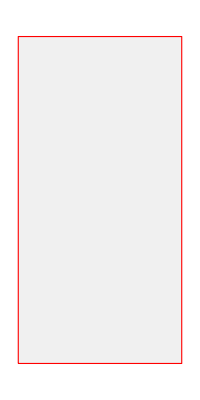
-Graphics- | -Graphics-(2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
0 | -2 | 5/2 | 3/2 | 2
0 | 1 | 5/2 | 1/2 | 5) | -Graphics- | • Scambia la seconda riga con la terza.
  In modo da ottenere -2 in posizione a_22.
 | -Graphics-

```mathematica
step1FirstString = {"A questo punto tutti gli elementi sotto il ",Style["pivot a_11", Bold, RGBColor[0.2,0.6,0.2]]," sono nulli (",Style["zero",Bold],").\nOra prendiamo in considerazione la posizione a_22 e gli elementi al di ", Style["sotto",Bold] ," di esso.\nQual è ",Style["l’elemento massimo in valore assoluto", Bold, Underlined] ," tra questi?\nÈ il ",Framed["-2", RoundingRadius->100, FrameStyle->Orange] ," in posizione a_32."};
step1FirstString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step1FirstString];
step1SecondString = {"• Scambia la seconda riga con la terza.\n  In modo da ottenere ", Framed["-2", RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_22."};
step1SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step1SecondString];
leftArrow = ImageResize[-Graphics-, {40,70}];
rightArrow =ImageResize[-Graphics-, {40,70}];
swapRows = ImageResize[-Graphics-,400];
matrixStep1= {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {0,Framed["-2", RoundingRadius->100, FrameStyle->Orange],5/2,3/2,2}, {0,1,5/2,1/2,5}} // MatrixForm;
rectangle = Rectangle[{0,0},{1,2}];
rectangleMatrix = Framed[Grid[{{Graphics[{EdgeForm[{Thick, Red}],RGBColor[0.94, 0.94, 0.94], rectangle}]}}, ItemSize->3.5, Frame -> True,FrameStyle->RGBColor[0.94,0.94,0.94], Spacings-> {2.5,0}], FrameStyle->None,FrameMargins->{{0,0},{0,33}}];
designedMatrix = Overlay[{rectangleMatrix, matrixStep1}, All, 2];

Framed[Grid[{{step1FirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left], FrameStyle->None, FrameMargins->{{0,0},{30,0}}]
matrixGrid = Grid[{{leftArrow, designedMatrix, rightArrow}}, Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24]];
Framed[Grid[{{matrixGrid,step1SecondString},{"", swapRows}}, Frame->None, ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}],FrameStyle->None, FrameMargins->{{0,0},{30,0}}]
```

```mathematica
backTag = "GaussPag10";
forwardTag = "GaussPag12";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag10Home.nb | IndietroHome.nbGaussPag10Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag12Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag12Home.nb

### Metodo di Gauss

#### Step 1 • Colonna 2

A questo punto tutti gli elementi sotto il pivot a_11 sono nulli (zero).
Ora prendiamo in considerazione la posizione a_22 e gli elementi al di sotto di essa.
Qual è l’elemento massimo in valore assoluto tra questi? È il -2 in posizione a_32.
Applichiamo la MOSSA 1.

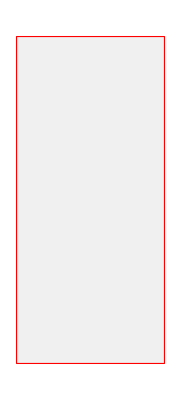
-Graphics-(2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | -5/2 | 3/2 | -3
0 | 1 | 5/2 | 1/2 | 5) | • Scambia la seconda riga con la terza.
  In modo da ottenere -2 in posizione a_22.
 | -Graphics-

```mathematica
step1FirstString = {"A questo punto tutti gli elementi sotto il ",Style["pivot a_11", Bold, RGBColor[0.2,0.6,0.2]]," sono nulli (",Style["zero",Bold],").\nOra prendiamo in considerazione la posizione a_22 e gli elementi al di ", Style["sotto",Bold] ," di essa.\nQual è ",Style["l’elemento massimo in valore assoluto", Bold, Underlined] ," tra questi? È il ",Framed["-2", RoundingRadius->100, FrameStyle->Orange] ," in posizione a_32.\nApplichiamo la ",Style["MOSSA 1", Bold],"."};
step1FirstString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step1FirstString];
step1SecondString = {"• Scambia la seconda riga con la terza.\n  In modo da ottenere ", Framed["-2", RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_22."};
step1SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step1SecondString];
swapRows = ImageResize[-Graphics-,400];
matrixStep1= {{Style[2, Bold, RGBColor[0.2,0.6,0.2]],0,3,-3,8},{0,Framed["-2", RoundingRadius->100, FrameStyle->Orange],5/2,3/2,2},{0,0,-5/2,3/2,-3}, {0,1,5/2,1/2,5}} // MatrixForm;
rectangle = Rectangle[{0,0},{0.5,1.1}];
rectangleMatrix = Framed[Grid[{{Graphics[{EdgeForm[{Thick, Red}],RGBColor[0.94, 0.94, 0.94], rectangle}]}}, ItemSize->3.5, Frame -> True,FrameStyle->RGBColor[0.94,0.94,0.94], Spacings-> {2.5,0}], FrameStyle->None,FrameMargins->{{0,0},{0,25}}];
designedMatrix = Overlay[{rectangleMatrix, matrixStep1}, All, 2];

Framed[Grid[{{step1FirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left], FrameStyle->None, FrameMargins->{{0,0},{30,0}}]
Framed[Grid[{{designedMatrix,step1SecondString},{"", swapRows}}, Frame->None, ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}],FrameStyle->None, FrameMargins->{{0,0},{30,0}}]
```

```mathematica
backTag = "GaussPag11";
forwardTag = "GaussPag13";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag11Home.nb | IndietroHome.nbGaussPag11Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag13Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag13Home.nb

### Metodo di Gauss

#### Step 2 • Colonna 2, Riga 3

```mathematica
normalOne = Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24];
pivotTwo = Style[2, Bold,RGBColor[0.2,0.6,0.2], FontFamily->"Roboto Condensed",FontSize->24];
step2FirstString = {"Il ", Style["primo elemento", Orange] ," sotto il ",Style["pivot a_22 = -2", Bold , RGBColor[0.2, 0.6, 0.2]]," è già nullo. ",Style["Non bisogna fare nessuna operazione",Bold,Underlined],"!"};
step2FirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ step2FirstString];

matrixStep2 = {{2,0,3,-3,8},{0,-2,5/2,3/2,2},{0,0,-5/2,3/2,-3}, {0,1,5/2,1/2,5}};
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,matrixStep2,{{1,Range[1,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{4,Range[3,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{Range[1,4],1}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{Range[2,3],Range[3,5]}}];
finalMatrixStep2 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2]]&,finalMatrixStep2,{{2,2}}];
finalMatrixStep2 = MapAt[Framed[#, FrameStyle->Orange]&,finalMatrixStep2,{{3,2}}];
finalMatrixStep2 = finalMatrixStep2 // MatrixForm;

elementsGrid = Grid[{{step3SecondString},{rightArrow}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24, TextAlignment-> Center], Alignment->{Center, Center}];
Grid[{{step2FirstString}, {Grid[{{finalMatrixStep2}}, ItemSize->Fit, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{0,5}]}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Left]
```

Il primo elemento sotto il pivot a_22 = -2 è già nullo. Non bisogna fare nessuna operazione!
(2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | -5/2 | 3/2 | -3
0 | 1 | 5/2 | 1/2 | 5)

```mathematica
backTag = "GaussPag12";
forwardTag = "GaussPag14";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag12Home.nb | IndietroHome.nbGaussPag12Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag14Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag14Home.nb

### Metodo di Gauss

#### Step 2 • Colonna 2, Riga 4

```mathematica
normalOne = Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24];
normalTwo = Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24];
normalThree = Style[3, FontFamily -> "Roboto Condensed", FontSize-> 24];
pivotTwo = Style[2, Bold,RGBColor[0.2,0.6,0.2], FontFamily->"Roboto Condensed",FontSize->24];
step2FirstString = {"Rendere nullo il ", Style["secondo elemento", Orange] ," sotto il ",Style["pivot a_22 = -2", Bold , RGBColor[0.2, 0.6, 0.2]]," ed effettuare la ",Style["MOSSA 2", Bold]," per ",Style["tutti", Bold,Underlined], " gli elementi della ",Style["stessa", Bold] ," riga."};
step2FirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ step2FirstString];
step3SecondString = {Style["MOSSA 2",Bold],"\nnuova R_4 : R_4 - ","(-",normalOne/pivotTwo,") R_2"};
step3SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step3SecondString];

matrixStep2 = {{2,0,3,-3,8},{0,-2,5/2,3/2,2},{0,0,-5/2,3/2,-3}, {0,0,5/2,1/2,5}};
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,matrixStep2,{{1,Range[1,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{4,Range[3,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{Range[1,4],1}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{Range[2,3],Range[3,5]}}];
finalMatrixStep2 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2]]&,finalMatrixStep2,{{2,2}}];
finalMatrixStep2 = MapAt[Framed[#, FrameStyle->Orange]&,finalMatrixStep2,{{4,2}}];
finalMatrixStep2 = finalMatrixStep2 // MatrixForm;

red1 = Style[15, Red, FontFamily -> "Roboto Condensed", FontSize-> 24];
red2 = Style[4, Red, FontFamily -> "Roboto Condensed", FontSize-> 24];
blue1 = Style[5, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue];
blue2 = Style[4, FontFamily -> "Roboto Condensed", FontSize-> 24,Blue];
purple1= Style[6,RGBColor[1,0,1]];
firstOperation = {Style[5, FontFamily -> "Roboto Condensed", FontSize-> 24]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24]," + ", normalOne /pivotTwo," × ",Style[5, FontFamily -> "Roboto Condensed", FontSize-> 24]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24]," = ", red1/red2};
firstOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ firstOperation];
secondOperation = {normalOne/normalTwo," + ",normalOne/pivotTwo," × ",normalThree/normalTwo," = ",blue1/blue2};
secondOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ secondOperation];
thirdOperation = {"5 + ",normalOne/pivotTwo," × 2 = ",purple1};
thirdOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ thirdOperation];
fourthOperation = {normalOne," + ",normalOne/pivotTwo," × (",-pivotTwo,") = ",Framed[0, FrameStyle->Orange]};
fourthOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ fourthOperation];

thirdMatrixStep2 = {{2,0,3,-3,8},{0,-2,5/2,3/2,2},{0,0,-5/2,3/2,-3}, {0,0,15/4,5/4,6}};
finalSecondMatrixStep2 = MapAt[Style[#, Red]&,thirdMatrixStep2,{{2,3},{4,3}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,3}}];
finalSecondMatrixStep2 = MapAt[Style[#, Blue]&,finalSecondMatrixStep2,{{2,4},{4,4}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,4}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[1,0,1]]&,finalSecondMatrixStep2,{{2,5},{4,5}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,5}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{1,Range[1,5]}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{2,1}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{3,Range[1,5]}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{4,2}}];
finalSecondMatrixStep2= MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2,0.4]]&,finalSecondMatrixStep2,{{2,2}}];

finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{4,1}}];
finalSecondMatrixStep2 = finalSecondMatrixStep2// MatrixForm;
rightArrow = ImageResize[-Graphics-,100];
elementsGrid = Grid[{{step3SecondString},{rightArrow}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24, TextAlignment-> Center], Alignment->{Center, Center}];
matrixGrid = Grid[{{finalMatrixStep2, elementsGrid, finalSecondMatrixStep2}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Spacings->{3,5}];
operationsGrid = Grid[{{fourthOperation,firstOperation,secondOperation,thirdOperation}},Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94], 
ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24],Spacings->{5,0} ];
Grid[{{step2FirstString}, {Grid[{{matrixGrid}}, ItemSize->Fit]},{Grid[{{operationsGrid}},ItemSize->Fit]}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Left]
```

Rendere nullo il secondo elemento sotto il pivot a_22 = -2 ed effettuare la MOSSA 2 per tutti gli elementi della stessa riga.
(2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | -5/2 | 3/2 | -3
0 | 0 | 5/2 | 1/2 | 5) | MOSSA 2
nuova R_4 : R_4 - (-1/2) R_2
-Graphics- | (2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | -5/2 | 3/2 | -3
0 | 0 | 15/4 | 5/4 | 6)
1 + 1/2 × (-2) = 0 | 5/2 + 1/2 × 5/2 = 15/4 | 1/2 + 1/2 × 3/2 = 5/4 | 5 + 1/2 × 2 = 6

```mathematica
backTag = "GaussPag13";
forwardTag = "GaussPag15";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag13Home.nb | IndietroHome.nbGaussPag13Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag15Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag15Home.nb

### Metodo di Gauss

#### Step 1 • Colonna 3

```mathematica
normalFifteen = Style[15, FontFamily -> "Roboto Condensed", FontSize-> 24];
normalFour = Style[4, FontFamily -> "Roboto Condensed", FontSize-> 24];
step1FirstString = {"A questo punto tutti gli elementi sotto il ",Style["pivot a_22", Bold, RGBColor[0.2,0.6,0.2]]," sono nulli (",Style["zero",Bold],").\nOra prendiamo in considerazione la posizione a_33 e l'elemento al di ", Style["sotto",Bold] ," di essa.\nE' ",Style["l’elemento massimo in valore assoluto", Bold, Underlined] ,"? No, è ",Framed[normalFifteen/normalFour, RoundingRadius->100, FrameStyle->Orange] ," in posizione a_43.\nApplichiamo la ",Style["MOSSA 1", Bold],"."};
step1FirstString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step1FirstString];
step1SecondString = {"• Scambia la terza riga con la quarta.\n  In modo da ottenere ", Framed[normalFifteen/normalFour, RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_33."};
step1SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step1SecondString];
leftArrow = ImageResize[-Graphics-, {40,60}];
rightArrow =ImageResize[-Graphics-, {40,60}];
swapRows = ImageResize[-Graphics-,400];
matrixStep1= {{2,0,3,-3,8},{0,Style[-2, Bold, RGBColor[0.2,0.6,0.2]],5/2,3/2,2},{0,0,-5/2,3/2,-3}, {0,0,Framed[15/4, RoundingRadius->100, FrameStyle->Orange],5/4,6}} // MatrixForm;
rectangle = Rectangle[{0,0},{1,2}];
rectangleMatrix = Framed[Grid[{{Graphics[{EdgeForm[{Thick, Red}],RGBColor[0.94, 0.94, 0.94], rectangle}]}}, ItemSize->3, Frame -> True,FrameStyle->RGBColor[0.94,0.94,0.94], Spacings-> {6.5,0}], FrameStyle->None,FrameMargins->{{0,0},{0,68}}];
designedMatrix = Overlay[{rectangleMatrix, matrixStep1}, All, 2];

Framed[Grid[{{step1FirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left], FrameStyle->None, FrameMargins->{{0,0},{30,0}}]
matrixGrid = Grid[{{Framed[leftArrow, FrameStyle->None,FrameMargins->{{0,0},{0,65}}], designedMatrix, Framed[rightArrow, FrameStyle->None,FrameMargins->{{0,0},{0,65}}]}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24]];
Framed[Grid[{{matrixGrid,step1SecondString},{"", swapRows}}, Frame->None, ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}],FrameStyle->None, FrameMargins->{{0,0},{30,0}}]
```

A questo punto tutti gli elementi sotto il pivot a_22 sono nulli (zero).
Ora prendiamo in considerazione la posizione a_33 e l'elemento al di sotto di essa.
E' l’elemento massimo in valore assoluto? No, è 15/4 in posizione a_43.
Applichiamo la MOSSA 1.

-Graphics- | -Graphics-(2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | -5/2 | 3/2 | -3
0 | 0 | 15/4 | 5/4 | 6) | -Graphics- | • Scambia la terza riga con la quarta.
  In modo da ottenere 15/4 in posizione a_33.
 | -Graphics-

```mathematica
backTag = "GaussPag14";
forwardTag = "GaussPag16";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag14Home.nb | IndietroHome.nbGaussPag14Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag16Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag16Home.nb

### Metodo di Gauss

#### Step 1 • Colonna 3

```mathematica
normalFifteen = Style[15, FontFamily -> "Roboto Condensed", FontSize-> 24];
normalFour = Style[4, FontFamily -> "Roboto Condensed", FontSize-> 24];
step1FirstString = {"A questo punto tutti gli elementi sotto il ",Style["pivot a_22", Bold, RGBColor[0.2,0.6,0.2]]," sono nulli (",Style["zero",Bold],").\nOra prendiamo in considerazione la posizione a_33 e l'elemento al di ", Style["sotto",Bold] ," di essa.\nE' ",Style["l’elemento massimo in valore assoluto", Bold, Underlined] ,"? No, è ",Framed[normalFifteen/normalFour, RoundingRadius->100, FrameStyle->Orange] ," in posizione a_43.\nApplichiamo la ",Style["MOSSA 1", Bold],"."};
step1FirstString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step1FirstString];
step1SecondString = {"• Scambia la terza riga con la quarta.\n  In modo da ottenere ", Framed[normalFifteen/normalFour, RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_33."};
step1SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step1SecondString];
swapRows = ImageResize[-Graphics-,400];
matrixStep1= {{2,0,3,-3,8},{0,Style[-2, Bold, RGBColor[0.2,0.6,0.2]],5/2,3/2,2},{0,0,Framed[15/4, RoundingRadius->100, FrameStyle->Orange],5/4,6},{0,0,-5/2,3/2,-3}} // MatrixForm;
rectangle = Rectangle[{0,0},{1,2}];
rectangleMatrix = Framed[Grid[{{Graphics[{EdgeForm[{Thick, Red}],RGBColor[0.94, 0.94, 0.94], rectangle}]}}, ItemSize->3, Frame -> True,FrameStyle->RGBColor[0.94,0.94,0.94], Spacings-> {6.5,0}], FrameStyle->None,FrameMargins->{{0,0},{0,68}}];
designedMatrix = Overlay[{rectangleMatrix, matrixStep1}, All, 2];

Framed[Grid[{{step1FirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left], FrameStyle->None, FrameMargins->{{0,0},{30,0}}]
Framed[Grid[{{designedMatrix,step1SecondString},{"", swapRows}}, Frame->None, ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}],FrameStyle->None, FrameMargins->{{0,0},{30,0}}]
```

A questo punto tutti gli elementi sotto il pivot a_22 sono nulli (zero).
Ora prendiamo in considerazione la posizione a_33 e l'elemento al di sotto di essa.
E' l’elemento massimo in valore assoluto? No, è 15/4 in posizione a_43.
Applichiamo la MOSSA 1.

-Graphics-(2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | 15/4 | 5/4 | 6
0 | 0 | -5/2 | 3/2 | -3) | • Scambia la terza riga con la quarta.
  In modo da ottenere 15/4 in posizione a_33.
 | -Graphics-

```mathematica
backTag = "GaussPag15";
forwardTag = "GaussPag17";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag15Home.nb | IndietroHome.nbGaussPag15Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag17Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag17Home.nb

### Metodo di Gauss

#### Step 2 • Colonna 3, Riga 4

```mathematica
greenFifteen = Style[15, FontFamily -> "Roboto Condensed", FontSize-> 24,Bold,RGBColor[0.2, 0.6, 0.2]];
greenFour = Style[4, FontFamily -> "Roboto Condensed", FontSize-> 24,Bold,RGBColor[0.2, 0.6, 0.2]];
normalFive= Style[5, FontFamily -> "Roboto Condensed", FontSize-> 24];
normalTwo = Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24];
normalThree = Style[3, FontFamily -> "Roboto Condensed", FontSize-> 24];
step2FirstString = {"Rendere nullo l'", Style["elemento", Orange] ," sotto il ",Style["pivot a_33 = ", Bold, RGBColor[0.2, 0.6, 0.2]],greenFifteen/greenFour," ed effettuare la ",Style["MOSSA 2", Bold]," per ",Style["tutti", Bold,Underlined], " gli elementi della ",Style["stessa", Bold] ," riga."};
step2FirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ step2FirstString];
step3SecondString = {Style["MOSSA 2",Bold],"\nnuova R_4 : R_4 - ","(-",normalFive/normalTwo," / ",greenFifteen/greenFour,") R_3 = R_4 + ",normalTwo/normalThree," R_3"};
step3SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step3SecondString];

matrixStep2 = {{2,0,3,-3,8},{0,-2,5/2,3/2,2},{0,0,15/4,5/4,6},{0,0,0,3/2,-3}} ;
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,matrixStep2,{{Range[1,2],Range[1,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{Range[3,4],Range[1,2]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{Range[3,4],Range[4,5]}}];
finalMatrixStep2 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2]]&,finalMatrixStep2,{{3,3}}];
finalMatrixStep2 = MapAt[Framed[#, FrameStyle->Orange]&,finalMatrixStep2,{{4,3}}];
finalMatrixStep2 = finalMatrixStep2 // MatrixForm;

red1 = Style[7, Red, FontFamily -> "Roboto Condensed", FontSize-> 24];
red2 = Style[3, Red, FontFamily -> "Roboto Condensed", FontSize-> 24];
blue1 = Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue];
firstOperation = {normalThree/normalTwo," + ", normalTwo /normalThree," × ",normalFive/normalFour," = ", red1/red2};
firstOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ firstOperation];
secondOperation = {"-3 + ",normalTwo/normalThree," × 6 = ",blue1};
secondOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ secondOperation];
thirdOperation = {-normalFive/normalTwo," + ",normalTwo/normalThree," × ",greenFifteen/greenFour," = ",Framed[0, FrameStyle->Orange]};
thirdOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ thirdOperation];

thirdMatrixStep2 = {{2,0,3,-3,8},{0,-2,5/2,3/2,2},{0,0,15/4,0,6},{0,0,0,7/3,1}}  ;
finalSecondMatrixStep2 = MapAt[Style[#, Red]&,thirdMatrixStep2,{{3,4},{4,4}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,4}}];
finalSecondMatrixStep2 = MapAt[Style[#, Blue]&,finalSecondMatrixStep2,{{3,5},{4,5}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,5}}];
finalSecondMatrixStep2 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2,0.4]]&,finalSecondMatrixStep2,{{3,3}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{Range[1,2],Range[1,5]}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{Range[3,4],Range[1,2]}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{4,3}}];
finalSecondMatrixStep2 = finalSecondMatrixStep2// MatrixForm;
rightArrow = ImageResize[-Graphics-,100];
elementsGrid = Grid[{{step3SecondString},{rightArrow}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24, TextAlignment-> Center], Alignment->{Center, Center}];
matrixGrid = Grid[{{finalMatrixStep2, elementsGrid, finalSecondMatrixStep2}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Spacings->{3,5}];
operationsGrid = Grid[{{thirdOperation,firstOperation,secondOperation}},Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94], 
ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24],Spacings->{5,0} ];
Grid[{{step2FirstString}, {Grid[{{matrixGrid}}, ItemSize->Fit]},{Grid[{{operationsGrid}},ItemSize->Fit]}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Left]
```

Rendere nullo l'elemento sotto il pivot a_33 = 15/4 ed effettuare la MOSSA 2 per tutti gli elementi della stessa riga.
(2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | 15/4 | 5/4 | 6
0 | 0 | 0 | 3/2 | -3) | MOSSA 2
nuova R_4 : R_4 - (-5/2 / 15/4) R_3 = R_4 + 2/3 R_3
-Graphics- | (2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | 15/4 | 0 | 6
0 | 0 | 0 | 7/3 | 1)
-5/2 + 2/3 × 15/4 = 0 | 3/2 + 2/3 × 5/4 = 7/3 | -3 + 2/3 × 6 = 1

```mathematica
backTag = "GaussPag16";
forwardTag = "GaussPag18";
exerciseTag = "ProvaTuMatriceGradini";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag16Home.nb | IndietroHome.nbGaussPag16Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuMatriceGradiniHome.nb | Prova tu!Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag18Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag18Home.nb

### Metodo di Gauss

#### Step 3

```mathematica
step3FirstString = {"La matrice ottenuta rappresenta un sistema ",Style["equivalente",Bold]," a quello di partenza, cioè ha le ",Style["stesse soluzioni",Underlined],".\nTornare ora alla rappresentazione del sistema con le equazioni ridotte."};
step3FirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ step3FirstString];

triangle = Triangle[{{0,0}, {0,4}, {4,0}}];
triangleMatrix = Grid[{{Graphics[{RGBColor[0.13,0.52,0.96, 0.2], triangle}]}}, ItemSize-> 7, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings -> {0.5,2}];
upperMatrix = highlightMatrixElements[{{2,0,3,-3,8}, {0,-2,5/2,3/2, 2}, {0,0,15/4,5/4,6}, {0,0,0,7/3,1}}] // MatrixForm;
upperMatrix = Overlay[{triangleMatrix, upperMatrix}, All, 2];

reducedSystem = Image[Import["images/sistema-gauss.png"],Magnification->0.45];
matrixGrid = Grid[{{Framed[upperMatrix,FrameStyle->None,FrameMargins->{{0,0},{0,20}}], "⟶",reducedSystem}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Spacings->{3,0}, Alignment->Center];
Grid[{{step3FirstString},{Framed[Grid[{{matrixGrid}},ItemSize->Fit],FrameStyle->None,FrameMargins->{{0,0},{0,50}}]}}, ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left]
```

La matrice ottenuta rappresenta un sistema equivalente a quello di partenza, cioè ha le stesse soluzioni.
Tornare ora alla rappresentazione del sistema con le equazioni ridotte.
-Graphics-(2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | 15/4 | 5/4 | 6
0 | 0 | 0 | 7/3 | 1) | ⟶ | -Graphics-

```mathematica
backTag = "GaussPag17";
forwardTag = "GaussPag19";
exerciseTag = "ProvaTuSistemaMatriceRidotta";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag17Home.nb | IndietroHome.nbGaussPag17Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuSistemaMatriceRidottaHome.nb | Prova tu!Home.nbProvaTuSistemaMatriceRidottaHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag19Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag19Home.nb

### Metodo di Gauss

#### Step 4

```mathematica
step4FirstString = "Risolvere il sistema partendo dall’equazione con una sola incognita.";
firstLinearSystem = Image[Import["images/sistemaIndietro1.png"],Magnification->0.5];
secondLinearSystem = Image[Import["images/sistemaIndietro2.png"],Magnification->0.5];
thirdLinearSystem = Image[Import["images/sistemaIndietro3.png"],Magnification->0.5];

systemGrid = Grid[{{firstLinearSystem,"⟶",secondLinearSystem,"⟶",secondLinearSystem}}, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,0}];
Grid[{{step4FirstString},{Framed[Grid[{{systemGrid}}, ItemSize->Fit], FrameStyle->None, FrameMargins->{{0,0},{30,60}}]}}, ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
```

Risolvere il sistema partendo dall’equazione con una sola incognita.
-Graphics- | ⟶ | -Graphics- | ⟶ | -Graphics-

```mathematica
backTag = "GaussPag18";
forwardTag = "GaussPag20";
exerciseTag = "ProvaTuSistemaMatriceRidotta";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag18Home.nb | IndietroHome.nbGaussPag18Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuSistemaMatriceRidottaHome.nb | Prova tu!Home.nbProvaTuSistemaMatriceRidottaHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag20Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag20Home.nb

### Metodo di Gauss

#### Step 4

```mathematica
step4FirstString = "Risolvere il sistema partendo dall’equazione con una sola incognita.";
fourthLinearSystem = Image[Import["images/sistemaIndietro4.png"],Magnification->0.5];
fifthLinearSystem = Image[Import["images/sistemaIndietro5.png"],Magnification->0.5];
sixthLinearSystem = Image[Import["images/sistemaIndietro6.png"],Magnification->0.5];

systemGrid = Grid[{{fourthLinearSystem,"⟶",fifthLinearSystem,"⟶",sixthLinearSystem}}, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,0}];
Grid[{{step4FirstString},{Framed[Grid[{{systemGrid}}, ItemSize->Fit], FrameStyle->None, FrameMargins->{{0,0},{30,60}}]}}, ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
```

Risolvere il sistema partendo dall’equazione con una sola incognita.
-Graphics- | ⟶ | -Graphics- | ⟶ | -Graphics-

```mathematica
backTag = "GaussPag19";
forwardTag = "GaussPag21";
exerciseTag = "ProvaTuSistemaMatriceRidotta";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag19Home.nb | IndietroHome.nbGaussPag19Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuSistemaMatriceRidottaHome.nb | Prova tu!Home.nbProvaTuSistemaMatriceRidottaHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag21Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag21Home.nb

### Metodo di Gauss

#### Step 4

```mathematica
step4FirstString = "Risolvere il sistema partendo dall’equazione con una sola incognita.";
seventhLinearSystem = Image[Import["images/sistemaIndietro7.png"],Magnification->0.5];
eighthLinearSystem = Image[Import["images/sistemaIndietro8.png"],Magnification->0.5];
ninethLinearSystem = Image[Import["images/sistemaIndietro9.png"],Magnification->0.5];

systemGrid = Grid[{{seventhLinearSystem,"⟶",eighthLinearSystem,"⟶",ninethLinearSystem}}, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,0}];
Grid[{{step4FirstString},{Framed[Grid[{{systemGrid}}, ItemSize->Fit], FrameStyle->None, FrameMargins->{{0,0},{30,60}}]}}, ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
```

Risolvere il sistema partendo dall’equazione con una sola incognita.
-Graphics- | ⟶ | -Graphics- | ⟶ | -Graphics-

```mathematica
backTag = "GaussPag20";
forwardTag = "GaussPag22";
exerciseTag = "ProvaTuSistemaMatriceRidotta";
navIndietroInizioEserciziAvanti
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbGaussPag20Home.nb | IndietroHome.nbGaussPag20Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbProvaTuSistemaMatriceRidottaHome.nb | Prova tu!Home.nbProvaTuSistemaMatriceRidottaHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag22Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag22Home.nb

### Metodo di Gauss

#### Sistemi impossibili

```mathematica
attentionImage  = -Graphics-;

zeroRed = Style[0, Red];
attention = Style["ATTENZIONE !", Red];
w = {Center,Left,Center,Center};
attentionText = "Non tutti i sistemi hanno soluzione.\nVediamo un esempio in cui accade questa cosa:";
attentionSystem= {3y-z==1,x+y+2z ==2,x+4y+z==0};
attentionMatrix= highlightMatrixElements[transformToMatrix[attentionSystem,True]];
firstMatrix = Permute[attentionMatrix,{2,1}]//MatrixForm;
sostitutionMatrix = highlightMatrixElements[{{1,1,2,2},{0,3,-1,1},{0,3,-1,-2}}]//MatrixForm;
sostitutionMatrix2 = {{1,1,2,2},{0,3,-1,1},{zeroRed,zeroRed,zeroRed,Style[-3, Red]}}//MatrixForm;
Grid[{{attentionImage, attentionText, SpanFromLeft, SpanFromLeft},{attention, displayEquationSystem[attentionSystem], "⟶", attentionMatrix//MatrixForm},{"","• Scambiare prima e seconda riga\n così da avere già 0 sotto l'elemento a_11",SpanFromLeft,firstMatrix},{"","• Sostituire: Nuova R3 : R3 - R1",SpanFromLeft ,sostitutionMatrix},{" ","• Sostituire: Nuova R3 : R3 - R2",SpanFromLeft,sostitutionMatrix2}}, Frame -> None, ItemSize-> {{Scaled[0.3],Scaled[0.3], Scaled[0.1], Scaled[0.3]}}, Spacings->{2, 2},Alignment->{w},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24]]
Grid[{{"Continua..."}}, ItemSize->Fit, Alignment->Right, ItemStyle->Directive[FontSize->24,FontFamily->"Roboto Condensed"],Spacings->{10,4},Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94]]
```

-Graphics- | Non tutti i sistemi hanno soluzione.
Vediamo un esempio in cui accade questa cosa: |  | 
ATTENZIONE ! | {3 y-z==1
x+y+2 z==2
x+4 y+z==0 | ⟶ | (0 | 3 | -1 | 1
1 | 1 | 2 | 2
1 | 4 | 1 | 0)
 | • Scambiare prima e seconda riga
 così da avere già 0 sotto l'elemento a_11 |  | (1 | 1 | 2 | 2
0 | 3 | -1 | 1
1 | 4 | 1 | 0)
 | • Sostituire: Nuova R3 : R3 - R1 |  | (1 | 1 | 2 | 2
0 | 3 | -1 | 1
0 | 3 | -1 | -2)
  | • Sostituire: Nuova R3 : R3 - R2 |  | (1 | 1 | 2 | 2
0 | 3 | -1 | 1
0 | 0 | 0 | -3)

Continua...

```mathematica
backTag = "GaussPag21";
forwardTag = "GaussPag23";
navAvantiInizioIndietro
Clear[backTag, forwardTag];
```

-Graphics-Home.nbGaussPag21Home.nb | IndietroHome.nbGaussPag21Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag23Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag23Home.nb

### Metodo di Gauss

#### Sistemi impossibili

```mathematica
attentionImage  = -Graphics-;
redArrow = -Graphics-;

zeroPink = Style[0, Red];
w = {Center, Center, Center, Center, Left};
attentionText = "Non tutti i sistemi hanno soluzione.\nVediamo un esempio in cui accade questa cosa:";
exampleSystemForm= {x+y+2z==2,3y-z ==1,HoldForm[0]==-3} ;
exampleMatrixForm= MatrixForm[{{1,1,2,2},{0,3,-1,1},{zeroPink,zeroPink,zeroPink,Style[-3,Red]}}];
Grid[{{attentionImage, attentionText, SpanFromLeft,SpanFromLeft,SpanFromLeft},{exampleMatrixForm,"⟶",displayEquationSystem[exampleSystemForm], redArrow,"Questo sistema è impossibile e\nnon ammette soluzioni."}}, Frame -> All,FrameStyle->RGBColor[0.94,0.94,0.94], ItemSize-> {{Scaled[0.3],Scaled[0.05], Scaled[0.3],Scaled[0.05], Scaled[0.3]}}, Spacings->{5, 4},Alignment-> {w},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24], Alignment->Center]
definitionString = "Quando i primi tre elementi di una riga sono 0 e l'ultimo è diverso da 0,\n il sistema è impossibile.";
Grid[{{definitionString}}, Frame->All, FrameStyle->RGBColor[1.0,0.0,0.0],ItemSize->Scaled[1],Spacings->{2,2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center]]
```

-Graphics- | Non tutti i sistemi hanno soluzione.
Vediamo un esempio in cui accade questa cosa: |  |  | 
(1 | 1 | 2 | 2
0 | 3 | -1 | 1
0 | 0 | 0 | -3) | ⟶ | {x+y+2 z==2
3 y-z==1
0==-3 | -Graphics- | Questo sistema è impossibile e
non ammette soluzioni.

Quando i primi tre elementi di una riga sono 0 e l'ultimo è diverso da 0,
 il sistema è impossibile.

```mathematica
backTag = "GaussPag22";
forwardTag = "GaussPag24";
navAvantiInizioIndietro
Clear[backTag, forwardTag];
```

-Graphics-Home.nbGaussPag22Home.nb | IndietroHome.nbGaussPag22Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag24Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag24Home.nb

### Metodo di Gauss

#### Sistemi indeterminati

```mathematica
handleWithCare = -Graphics-;
zeroBlue= Style[0, Blue]; 
w = {Center, Left, Center, Center};
alarmText = Style["TRATTARE CON CAUTELA !", Blue];
exampleText = "Vediamo un esempio in cui un sistema non ha una sola soluzione.";
attentionSystem= {3y-z==1,x+y+2z ==2,x+4y+z==3};
attentionMatrix= highlightMatrixElements[transformToMatrix[attentionSystem,True]];
firstMatrix = Permute[attentionMatrix, {2,1}]//MatrixForm;
sostitutionMatrix =highlightMatrixElements[{{1,1,2,2},{0,3,-1,1},{0,3,-1,1}}]//MatrixForm;
sostitutionMatrix2 = MatrixForm[{{1,1,2,2},{0,3,-1,1},{zeroBlue,zeroBlue,zeroBlue,zeroBlue}}];
Grid[{{handleWithCare, exampleText, SpanFromLeft, SpanFromLeft},{alarmText, displayEquationSystem[attentionSystem], "⟶", attentionMatrix//MatrixForm},{" ","• Scambiare prima e seconda riga\n così da avere già 0 sotto l'elemento a_11",SpanFromLeft,firstMatrix},{"","• Sostituire: Nuova R3 : R3 - R1",SpanFromLeft ,sostitutionMatrix},{"","• Sostituire: Nuova R3 : R3 - R2",SpanFromLeft,sostitutionMatrix2}}, Frame -> None, ItemSize-> {{Scaled[0.3],Scaled[0.3], Scaled[0.1], Scaled[0.3]}}, Spacings->{2, 2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24], Alignment->{w}]
Grid[{{"Continua..."}}, ItemSize->Fit, Alignment->Right, ItemStyle->Directive[FontSize->24,FontFamily->"Roboto Condensed"],Spacings->{10,4},Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94]]
```

-Graphics- | Vediamo un esempio in cui un sistema non ha una sola soluzione. |  | 
TRATTARE CON CAUTELA ! | {3 y-z==1
x+y+2 z==2
x+4 y+z==3 | ⟶ | (0 | 3 | -1 | 1
1 | 1 | 2 | 2
1 | 4 | 1 | 3)
  | • Scambiare prima e seconda riga
 così da avere già 0 sotto l'elemento a_11 |  | (1 | 1 | 2 | 2
0 | 3 | -1 | 1
1 | 4 | 1 | 3)
 | • Sostituire: Nuova R3 : R3 - R1 |  | (1 | 1 | 2 | 2
0 | 3 | -1 | 1
0 | 3 | -1 | 1)
 | • Sostituire: Nuova R3 : R3 - R2 |  | (1 | 1 | 2 | 2
0 | 3 | -1 | 1
0 | 0 | 0 | 0)

Continua...

```mathematica
backTag = "GaussPag23";
forwardTag = "GaussPag25";
navAvantiInizioIndietro
Clear[backTag, forwardTag];
```

-Graphics-Home.nbGaussPag23Home.nb | IndietroHome.nbGaussPag23Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag25Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag25Home.nb

### Metodo di Gauss

#### Sistemi indeterminati

```mathematica
handleWithCare = -Graphics-;
rightArrow = -Graphics-;
zeroBlue = Style[0,Blue];
w = {Center, Center, Center, Center, Left};
exampleText = "Vediamo un esempio in cui un sistema non ha solo una soluzione.";
exampleSystemForm= {x+y+2z==2,3y-z ==1,HoldForm [0]==0} ;
exampleMatrixForm= MatrixForm[{{1,1,2,2},{0,3,-1,1},{zeroBlue,zeroBlue,zeroBlue,zeroBlue}}];
Grid[{{handleWithCare,exampleText, SpanFromLeft,SpanFromLeft,SpanFromLeft},{exampleMatrixForm,"⟶",displayEquationSystem[exampleSystemForm],rightArrow, "Questo sistema è indeterminato e\nammette infinite soluzioni."}}, Frame -> All,FrameStyle->RGBColor[0.94,0.94,0.94], ItemSize-> {{Scaled[0.25],Scaled[0.05], Scaled[0.25],Scaled[0.05], Scaled[0.4]}}, Spacings->{5, 4},Alignment-> {w},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24], Alignment->Center]
 definitionString = "Quando tutti gli elementi di una riga sono 0 il sistema è indeterminato.";
Grid[{{definitionString}}, Frame->All, FrameStyle->RGBColor[0.0,0.0,1.0],ItemSize->Scaled[1],Spacings->{2,2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center]]
```

-Graphics- | Vediamo un esempio in cui un sistema non ha solo una soluzione. |  |  | 
(1 | 1 | 2 | 2
0 | 3 | -1 | 1
0 | 0 | 0 | 0) | ⟶ | {x+y+2 z==2
3 y-z==1
0==0 | -Graphics- | Questo sistema è indeterminato e
ammette infinite soluzioni.

Quando tutti gli elementi di una riga sono 0 il sistema è indeterminato.

```mathematica
backTag = "GaussPag24";
forwardTag = "GaussPag26";
navAvantiInizioIndietro
Clear[backTag, forwardTag];
```

-Graphics-Home.nbGaussPag24Home.nb | IndietroHome.nbGaussPag24Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbGaussPag26Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag26Home.nb

### Metodo di Gauss

#### Conclusione

```mathematica
endText = "Abbiamo illustrato l’algoritmo di Gauss tramite esempi,\n ma è un metodo che funziona in generale per qualsiasi matrice. \nCon un opportuno uso delle «mosse» elementari è possibile ridurre a gradini matrici anche di dimensioni m x n.";
Grid[{{endText}}, Frame->All, FrameStyle->RGBColor[1.0,0.0,0.0],ItemSize->Scaled[1],Spacings->{3,3},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center]]
```

Abbiamo illustrato l’algoritmo di Gauss tramite esempi,
 ma è un metodo che funziona in generale per qualsiasi matrice. 
Con un opportuno uso delle «mosse» elementari è possibile ridurre a gradini matrici anche di dimensioni m x n.

```mathematica
backTag = "MatriciPag25";
navIndietroInizio
Clear[backTag];
```

-Graphics-Home.nbMatriciPag25Home.nb | IndietroHome.nbMatriciPag25Home.nbHyperlinkHyperlinkActive | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb

### Esercizi

#### Su quale tipo di esercizio ti vuoi esercitare?

```mathematica
firstStringExercixe=Style["Quiz sulle matrici", Bold, FontSize->24,FontFamily->"Roboto Condensed",TextAlignment->Center];
secondStringExercise=Style["Passaggi del metodo di Gauss",Bold, FontSize->24,FontFamily->"Roboto Condensed",TextAlignment->Center];
secondStringExercise1=Style["Trasposizione di un sistema\nlineare nella matrice associata", FontSize->18, Italic,FontFamily->"Roboto Condensed",TextAlignment->Center];
secondStringExercise2=Style["Ridurre una matrice a gradini\n",FontSize->18, Italic,FontFamily->"Roboto Condensed",TextAlignment->Center];
secondStringExercise3=Style["Trasposizione di una matrice a\ngradini nel sistema lineare associato",FontSize->18, Italic,FontFamily->"Roboto Condensed",TextAlignment->Center];
thirdStringExercise1=Style["Verifica Finale",Bold, FontSize->24,FontFamily->"Roboto Condensed",TextAlignment->Center];
thirdStringExercise2=Style["Risolvi un sistema lineare con il metodo di Gauss",FontSize->18, Italic,FontFamily->"Roboto Condensed",TextAlignment->Center];
Grid[{{
Hyperlink[Button[Text[Grid[{{-Graphics-},{secondStringExercise},{secondStringExercise1}},ItemSize-> Fit,Spacings->{Automatic, {2,1,1}}]],ImageSize->Scaled[1],FrameMargins->28],{"Home.nb", "ProvaTuSistemaMatrice"},BaseStyle->Black],
Hyperlink[Button[Text[Grid[{{-Graphics-},{secondStringExercise},{secondStringExercise2}},ItemSize-> Fit,Spacings->{Automatic,{2,2,1}}]],ImageSize->Scaled[1],FrameMargins->25],{"Home.nb", "ProvaTuMatriceGradini"}, BaseStyle->Black],
Hyperlink[Button[Text[Grid[{{-Graphics-},{secondStringExercise},{secondStringExercise3}},ItemSize-> Fit,Spacings->{Automatic,{2,1,1}}]],ImageSize->Scaled[1],FrameMargins->28], {"Home.nb", "ProvaTuSistemaMatriceRidotta"}, BaseStyle->Black]
}},ItemSize-> {{Scaled[0.33],Scaled[0.34], Scaled[0.33]}}]

Grid[{{
Hyperlink[Button[Text[Grid[{{-Graphics-},{firstStringExercixe},{}},Spacings->{Automatic,{2,2,1}}]],ImageSize->Scaled[1],FrameMargins->20],{"Home.nb","ProvaTuDomandeTeoria"},BaseStyle->Black],
Hyperlink[Button[Text[Grid[{{-Graphics-},{thirdStringExercise1},{thirdStringExercise2}},Spacings->{Automatic,{2,1,1}}]],ImageSize->Scaled[1],FrameMargins->15],{"Home.nb", "ProvaTuEsercizioFinale"},BaseStyle->Black]
}},ItemSize-> {{Scaled[0.5],Scaled[0.5]}}]
```

-Graphics-
Passaggi del metodo di Gauss
Trasposizione di un sistema
lineare nella matrice associataHome.nbProvaTuSistemaMatriceHome.nbHyperlinkHyperlinkActive | -Graphics-
Passaggi del metodo di Gauss
Ridurre una matrice a gradini
Home.nbProvaTuMatriceGradiniHome.nbHyperlinkHyperlinkActive | -Graphics-
Passaggi del metodo di Gauss
Trasposizione di una matrice a
gradini nel sistema lineare associatoHome.nbProvaTuSistemaMatriceRidottaHome.nbHyperlinkHyperlinkActive

-Graphics-
Quiz sulle matrici
Home.nbProvaTuDomandeTeoriaHome.nbHyperlinkHyperlinkActive | -Graphics-
Verifica Finale
Risolvi un sistema lineare con il metodo di GaussHome.nbProvaTuEsercizioFinaleHome.nbHyperlinkHyperlinkActive

```mathematica
navInizio
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive

### Prova Tu: da sistema lineare a matrice

#### Guarda il sistema lineare che ti viene presentato e prova ad inserire i relativi coefficienti e termini noti nella matrice a fianco. Quando sei pronto, clicca su “Verifica!” per controllare il risultato oppure clicca su “Ricomincia” per provare con un altro sistema.

```mathematica
exerciseSystemToMatrix[]
```

```mathematica
exerciseTag= "Esercizi";
backTag = "MatriciPag1";
backButton := Hyperlink[Button[Image[Import["images/home.png"],ImageSize->{50,50}], Appearance->{None}, ImageSize->{50,50}],{"Home.nb",backTag}];
backLink := Hyperlink["Torna alla Teoria", {"Home.nb", backTag},BaseStyle->RGBColor[0.2,0.6,0.86]];
exerciseBackLink := Hyperlink["Torna agli Esercizi", {"Home.nb", exerciseTag}, BaseStyle->RGBColor[0.2,0.6,0.86]];
navEsercizi := Grid[{{exerciseButton, exerciseBackLink,backLink,backButton}},Alignment->{{Right,Left,Right,Left}}, ItemSize->{{Scaled[0.05],Scaled[0.45],Scaled[0.45],Scaled[0.05]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navEsercizi
Clear[backTag,exerciseTag];
```

-Graphics-Home.nbEserciziHome.nb | Torna agli EserciziHome.nbEserciziHome.nbHyperlinkHyperlinkActive | Torna alla TeoriaHome.nbMatriciPag1Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag1Home.nb

### Prova Tu: Domande sulla Teoria

```mathematica
questionsExercise[]
```

```mathematica
exerciseTag = "Esercizi";
backTag = "MatriciPag1";
navEsercizi
Clear[exerciseTag,backTag];
```

-Graphics-Home.nbEserciziHome.nb | Torna agli EserciziHome.nbEserciziHome.nbHyperlinkHyperlinkActive | Torna alla TeoriaHome.nbMatriciPag1Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag1Home.nb

### Prova Tu: Sistema associato alla matrice ridotta

#### Partendo dalla matrice ridotta usando gli step e le mosse di Gauss, scrivi ogni equazione del sistema associato

RICORDA: La matrice è completa e sono evidenziati i coefficienti (blu) ed i termini noti (verde)!

```mathematica
exerciseReducedMatrixToSystem[]
```

```mathematica
exerciseTag = "Esercizi";
backTag = "GaussPag18";
navEsercizi
Clear[exerciseTag,backTag];
```

-Graphics-Home.nbEserciziHome.nb | Torna agli EserciziHome.nbEserciziHome.nbHyperlinkHyperlinkActive | Torna alla TeoriaHome.nbGaussPag18Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag18Home.nb

### Prova Tu: Metodo di Gauss

#### Rendi questa matrice a gradini attraverso gli step e usando le mosse di Gauss che hai visto nella teoria.

RICORDA: La matrice è completa e sono evidenziati i coefficienti (blu) ed i termini noti (verde)!

```mathematica
exerciseTriangularizeMatrix[getRandomSystem[]]
```

```mathematica
exerciseTag = "Esercizi";
backTag = "GaussPag5";
navEsercizi
Clear[exerciseTag,backTag];
```

-Graphics-Home.nbEserciziHome.nb | Torna agli EserciziHome.nbEserciziHome.nbHyperlinkHyperlinkActive | Torna alla TeoriaHome.nbGaussPag5Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbGaussPag5Home.nb

### Mani all’opera!

#### Scrivere sottotitolo QUI!

### Appendice

```mathematica
Grid[{{"Questo progetto è stato pensato per i ragazzi del primo biennio dei licei scientifici e degli istituti tecnici"}}, Frame->All, FrameStyle->RGBColor[1.0,0.0,0.0],ItemSize->Scaled[1],Spacings->{2,2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left]]
```

Questo progetto è stato pensato per i ragazzi del primo biennio dei licei scientifici e degli istituti tecnici

#### Problemi informatici

Quando si inserisce una equazione in Mathematica, il kernel la memorizza riordinandola e risolvendola con le informazioni che possiede. Questo ha causato alcuni problemi:

Non è possibile utilizzare le incognite in ordine non alfabetico; ad esempio, non si possono utilizzare le combinazioni di x, y, z, t nè quelle di x, y, z, w. Non siamo riusciti a risolvere questo problema; per questo è  stato necessario spiegare nelle slide che, nel  momento in cui lo studente volesse inserire manualmente le equazioni, queste devono avere incognite già ordinate in ordine alfabetico.

Non siamo riusciti a definire dei sistemi in cui le incognite compaiono in entrambi i membri delle equazioni: in esercizi ed esempi tutti i termini con le incognite compaiono a sinistra dell’uguale mentre il termine noto è l’unico termine a destra dell’uguale. A causa di ciò non siamo riusciti a creare sistemi più complicati sui quali gli studenti possano fare esercizi.

Quando chiediamo all’utente di passare dalla notazione matriciale al sitema associato, lo studente deve necessariamente inserire l’equazione nella forma ax+by+...=c. Se prova, invece, ad inserire l’equazione associata ad una riga della matrice nella forma equivalente ax+by+...-c=0  il kernel non riesce a riconoscere l’equivalenza e restituisce un errore.

Mathematica non implementa la funzione che riduce una matrice attraverso fattorizzazione LU con pivoting parziale. Abbiamo risolto questo problema implementando a mano la funzione.

L’implementazione della Fattorizzazione LU fatta non effettua controlli specifici su un pivot nullo. Inizialmente, infatti, viene calcolato il determinante della matrice in input: nel caso sia pari a 0, l’algoritmo termina ritornando una tupla di elementi nulli; così facendo, si evita che un pivot possa essere nullo durante il calcolo.

#### Problemi matematici

La notazione matriciale è molto complessa da spiegare a parole; la traduzione da linguaggio matematico a linguaggio naturale, infatti, perde di precisione e chiarezza per cui ci è risultato difficile riuscire a mantenere corretta la traduzione.

L’algoritmo di Gauss richiede un certo livello di astrazione nei passaggi che non è facile da riportare in slide a scopo didattico. Per questo motivo, è stato scelto di mostrare molteplici slide chiare e pulite per evidenziare al meglio i concetti.

Deve essere introdotta una parte consistente di teoria e ci è sembrato opportuna farlo tramite esempi. Se avessimo lavorato con la notazione letterale pura il tutto sarebbe risultato troppo pesante e di difficile comprensione per gli studenti.

```mathematica
homeButton = Hyperlink[Button[Image[Import["images/home.png"],ImageSize->{50,50}], Appearance->{None}, ImageSize->{50,50}],{"Home.nb","Homepage"}];
homeLink := Hyperlink["Torna Indietro", {"Home.nb", "Homepage"},BaseStyle->RGBColor[0.2,0.6,0.86]];
navIndietroHome := Grid[{{homeButton,homeLink}},Alignment->{{Right, Left}}, ItemSize->{{Scaled[0.05],Scaled[0.95]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{2,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navIndietroHome
```

-Graphics-Home.nbHomepageHome.nb | Torna IndietroHome.nbHomepageHome.nbHyperlinkHyperlinkActive

### Bibliografia

#### Manuali

Bergamini, Trifone, Barozzi. Matematica Blu (Capitolo 10). Zanichelli Editore, Bologna. 2010.
http://online.scuola.zanichelli.it/bergamini-files/Biennio/Capitoli/BLU/bergamini_capitolo_ 10_blu.pdf

Appunti universitari di Calcolo Numerico, Algebra e Geometria.

#### Sitografia

http://reference.wolfram.com/language/

www.matematicamente.it

www.youmath.it

```mathematica
navIndietroHome
```

-Graphics-Home.nbHomepageHome.nb | Torna IndietroHome.nbHomepageHome.nbHyperlinkHyperlinkActive